```mathematica
λ=0.6143*I;
soluciones=Solve[-2 (λ+λ^3)+(3+9 λ^2) z-12 λ z^2+(3+λ^2) z^3==0,z]
z1=z/.soluciones[[1]]
z2=z/.soluciones[[2]]
z3=z/.soluciones[[3]]
```

{{z→0.-0.283576 ⅈ},{z→0.+0.378772 ⅈ},{z→0.+2.71556 ⅈ}}

0.-0.283576 ⅈ

0.+0.378772 ⅈ

0.+2.71556 ⅈ

```mathematica
p[z_]:=(z^2-1)(z-λ);lp[z_]=p[z]p''[z]/p'[z]/p'[z];sp[z_]=z-1/(1-lp[z])p[z]/p'[z];
iterSch= Compile[{{z,_Complex}},sp[z]];
r1=1;r2=-1;r3=λ;
Clear[rootPosition]
rootPosition[z_]:= 
Which[Abs[z - r1] <  10.0^(-6), 3,
	       Abs[z - r2] <  10.0^(-6), 2,
	       Abs[z -r3] <  10.0^(-6), 1,
	       True, 0]
Clear[iterColorAlgorithm,colorLevel,fractalColor,plotColorFractal]
iterColorAlgorithm[iterMethod_,x_,y_,lim_] :=
Block[{z,ct,r}, z = x + y I; ct = 0;r = rootPosition[z];
While[(r==0) && (ct < lim),++ct;
z = iterMethod[z];r = rootPosition[z]
];
If[Head[r]==Which,r =0]; (* "Which" unevaluated *)
Return[N[r+ct/(lim+0.001)]]
]
colorLevelWS= Compile[{{p,_Real}},0.4*FractionalPart[p]];
fractalColorWS[p_] :=
Block[{pp = colorLevelWS[p]},
Switch[IntegerPart[p],
3, CMYKColor[0.6+pp,0.,0.,2*pp],
2, CMYKColor[0.,0.6+pp,0.,2*pp],
1, CMYKColor[0.,0.,0.6+pp,2*pp],
0, CMYKColor[0.,0.,0.,1.]
]
]
ft[min_,max_,pt_,nTicks_]:=Block[{taux,j,stepTicks=(max-min)/(nTicks-1)},
taux=Table[{pt*(j-1)/(nTicks-1)+1,min+(j-1)*stepTicks},{j,1,nTicks}]
]
plotColorFractal[iterMethod_,points_]:=
Block[{$Messages = {},
stepx=(xxMax-xxMin)/points,stepy=(yyMax-yyMin)/points},
ArrayPlot[Table[iterColorAlgorithm[iterMethod,x,y,limIterations],
{y,yyMax,1.00001*yyMin,-stepy},
{x,xxMin,1.00001*xxMax,stepx}],
FrameTicks->{ft[yyMax,yyMin,points,5],ft[xxMin,xxMax,points,5]},
PlotRange->{0,4},(* Three roots *)
ColorFunctionScaling->False,
ColorFunction->fractalColorWS
]
]
```

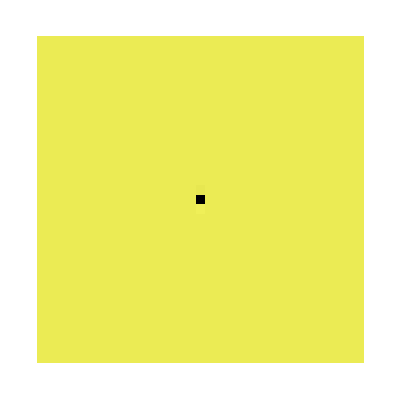

```mathematica
numberPoints =32;
limIterations=50;
xxMin=-300.; xxMax=300; yyMin=-300; yyMax=300;
plotColorFractal[iterSch, numberPoints]
```

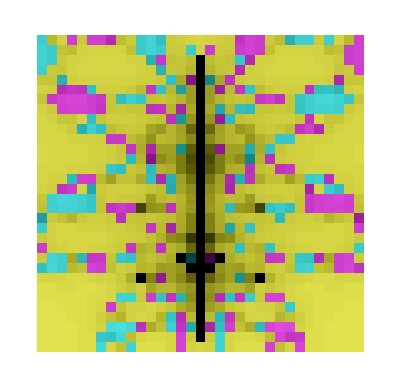

```mathematica
numberPoints =32;
limIterations=50;
xxMin=Re[z3]-1; xxMax=Re[z3]+1; yyMin=Im[z3]-1; yyMax=Im[z3]+2.75;
plotColorFractal[iterSch, numberPoints]
```

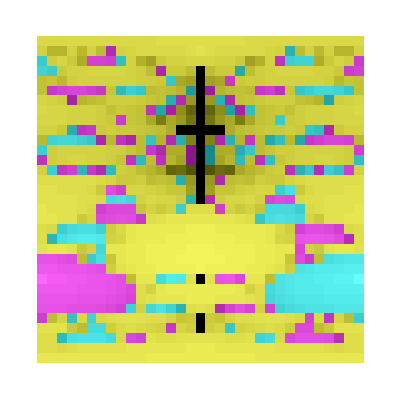

```mathematica
numberPoints =32;
limIterations=50;
xxMin=-1; xxMax=1; yyMin=-2; yyMax=6;
plotColorFractal[iterSch, numberPoints]
```

```mathematica
NestList[sp,z1,100]
```

{0.-0.283576 ⅈ,0.-5.17277 ⅈ,0.+0.4673 ⅈ,0.+0.600761 ⅈ,0.+0.61414 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ}

```mathematica
NestList[sp,z2,100]
```

{0.+0.378772 ⅈ,0.+0.593128 ⅈ,0.+0.613913 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ,0.+0.6143 ⅈ}

```mathematica
NestList[sp,z3,50000]
```

```mathematica
NestList[sp,-17/2*I,100]
```

{-(17 ⅈ)/2,0.+0.473137 ⅈ,0.+1.21244 ⅈ,0.-5.11115 ⅈ,0.+0.502294 ⅈ,0.+1.33623 ⅈ,0.-3.36606 ⅈ,0.+0.700725 ⅈ,0.+2.73825 ⅈ,0.-0.80203 ⅈ,0.-4.52344 ⅈ,0.+0.542574 ⅈ,0.+1.52957 ⅈ,0.-2.25331 ⅈ,0.+1.13582 ⅈ,0.-7.76285 ⅈ,0.+0.46118 ⅈ,0.+1.16499 ⅈ,0.-6.46501 ⅈ,0.+0.460623 ⅈ,0.+1.16282 ⅈ,0.-6.54561 ⅈ,0.+0.459722 ⅈ,0.+1.15932 ⅈ,0.-6.68009 ⅈ,0.+0.458533 ⅈ,0.+1.15472 ⅈ,0.-6.86648 ⅈ,0.+0.457497 ⅈ,0.+1.15072 ⅈ,0.-7.03735 ⅈ,0.+0.457137 ⅈ,0.+1.14934 ⅈ,0.-7.0987 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09838 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ}

```mathematica
lista={0.+2.6496388031605695 ⅈ,0.-0.038256572464081096 ⅈ,0.+4.481624687408443 ⅈ,0.+0.005015269595079808 ⅈ,0.+2.3603649862451115 ⅈ,0.-0.03158862708465371 ⅈ,0.+3.978034379287431 ⅈ,0.-0.009832480342556682 ⅈ,0.+2.8535705737968766 ⅈ,0.-0.03775995702562085 ⅈ,0.+4.440460993459056 ⅈ,0.+0.0038331974327325824 ⅈ,0.+2.3941765858247654 ⅈ,0.-0.03299050436357742 ⅈ,0.+4.075692809300733 ⅈ,0.-0.006904387096736464 ⅈ,0.+2.74320565907016 ⅈ,0.-0.038417646396329275 ⅈ,0.+4.49511545576266 ⅈ,0.+0.005401103223627857 ⅈ,0.+2.3495042282547103 ⅈ,0.-0.031094951212500277 ⅈ,0.+3.944582717972388 ⅈ,0.-0.01083716875913554 ⅈ,0.+2.893176969507961 ⅈ,0.-0.03733932377836657 ⅈ,0.+4.406095531699306 ⅈ,0.+0.0028409677227791974 ⅈ,0.+2.4231990538589674 ⅈ,0.-0.03403950822595503 ⅈ,0.+4.1514580304458395 ⅈ,0.-0.00464286799766267 ⅈ,0.+2.662802876086372 ⅈ,0.-0.03832527844265288 ⅈ,0.+4.4873707309658215 ⅈ,0.+0.005179701684136617 ⅈ,0.+2.3557259888818494 ⅈ,0.-0.03138041626838328 ⅈ,0.+3.9638676156289776 ⅈ,0.-0.010257921768690004 ⅈ,0.+2.8702298390236614 ⅈ,0.-0.037593750407018955 ⅈ,0.+4.426827747445133 ⅈ,0.+0.0034401410628710494 ⅈ,0.+2.4056023668324964 ⅈ,0.-0.03341992473850919 ⅈ,0.+4.106422575275047 ⅈ,0.-0.005985763633318264 ⅈ,0.+2.7100578779916074 ⅈ,0.-0.03844458254351757 ⅈ,0.+4.497378239427937 ⅈ,0.+0.00546574112924425 ⅈ,0.+2.3476930676226893 ⅈ,0.-0.031010501105968036 ⅈ,0.+3.938908010082749 ⅈ,0.-0.01100762639349906 ⅈ,0.+2.899988704168805 ⅈ,0.-0.03725832029318843 ⅈ,0.+4.399529489596215 ⅈ,0.+0.002650846291093245 ⅈ,0.+2.428828351531742 ⅈ,0.-0.03422730039599342 ⅈ,0.+4.165273599269231 ⅈ,0.-0.004231821854573603 ⅈ,0.+2.648616317961881 ⅈ,0.-0.03825055801757893 ⅈ,0.+4.481122280792311 ⅈ,0.+0.005000885676498257 ⅈ,0.+2.3607715283837885 ⅈ,0.-0.031606686706852294 ⅈ,0.+3.9792672026832223 ⅈ,0.-0.0097954619372711 ⅈ,0.+2.852128736546007 ⅈ,0.-0.03777358598765623 ⅈ,0.+4.441582087563454 ⅈ,0.+0.0038654853313824233 ⅈ,0.+2.3932421083713726 ⅈ,0.-0.032954417589331264 ⅈ,0.+4.073128152296121 ⅈ,0.-0.006981127729845937 ⅈ,0.+2.746005757523506 ⅈ,0.-0.03841145535247881 ⅈ,0.+4.494595647950387 ⅈ,0.+0.005386251422495825 ⅈ,0.+2.349920713376848 ⅈ,0.-0.03111428439876862 ⅈ,0.+3.9458837764333854 ⅈ,0.-0.010798087690677693 ⅈ,0.+2.8916190346868675 ⅈ,0.-0.03735750395545967 ⅈ,0.+4.407571483045096 ⅈ,0.+0.002883680679167888 ⅈ,0.+2.4219374162676677 ⅈ,0.-0.03399673609177878 ⅈ,0.+4.148322212013404 ⅈ,0.-0.004736229159863825 ⅈ,0.+2.666042986280567 ⅈ,0.-0.038339738289297376 ⅈ,0.+4.4885816385726685 ⅈ,0.+0.005214335528379799 ⅈ,0.+2.3547508691441 ⅈ,0.-0.031336148664064645 ⅈ,0.+3.9608666299051767 ⅈ,0.-0.010348054298626064 ⅈ,0.+2.873780278134854 ⅈ,0.-0.03755628514994491 ⅈ,0.+4.423764451873485 ⅈ,0.+0.003351719377736373 ⅈ,0.+2.408185478733888 ⅈ,0.-0.033514014674019155 ⅈ,0.+4.113208208544409 ⅈ,0.-0.005783153268857255 ⅈ,0.+2.7028378359040186 ⅈ,0.-0.03843872621378708 ⅈ,0.+4.496886110872618 ⅈ,0.+0.005451685051070854 ⅈ,0.+2.3480867180259746 ⅈ,0.-0.031028908196190752 ⅈ,0.+3.940143714944589 ⅈ,0.-0.010970508016269864 ⅈ,0.+2.89850309806149 ⅈ,0.-0.03727619580960839 ⅈ,0.+4.400977026241215 ⅈ,0.+0.0026927747747977904 ⅈ,0.+2.42758498462313 ⅈ,0.-0.034186249279050784 ⅈ,0.+4.162246883397196 ⅈ,0.-0.004321834482243325 ⅈ,0.+2.6517120075280087 ⅈ,0.-0.038268464948136405 ⅈ,0.+4.4826183880256885 ⅈ,0.+0.0050437160799603475 ⅈ,0.+2.359561335340878 ⅈ,0.-0.03155283843883305 ⅈ,0.+3.9755932094194386 ⅈ,0.-0.009905784505301884 ⅈ,0.+2.856429342838429 ⅈ,0.-0.037732574495429994 ⅈ,0.+4.438210009187581 ⅈ,0.+0.0037683526154888014 ⅈ,0.+2.396055202006066 ⅈ,0.-0.033062605913482646 ⅈ,0.+4.080825207080585 ⅈ,0.-0.006750846012359979 ⅈ,0.+2.7376177313535126 ⅈ,0.-0.0384282168394976 ⅈ,0.+4.4960031998488255 ⅈ,0.+0.005426464876406634 ⅈ,0.+2.3487933086574855 ⅈ,0.-0.031061875731063004 ⅈ,0.+3.942358531636886 ⅈ,0.-0.010903978973890727 ⅈ,0.+2.8958435845077437 ⅈ,0.-0.037307905699428545 ⅈ,0.+4.403546845261478 ⅈ,0.+0.002767190173746492 ⅈ,0.+2.4253808961462697 ⅈ,0.-0.03411288442606608 ⅈ,0.+4.156846940129768 ⅈ,0.-0.004482480637919117 ⅈ,0.+2.6572521301181693 ⅈ,0.-0.038298269834574405 ⅈ,0.+4.485110443083643 ⅈ,0.+0.005115036975579024 ⅈ,0.+2.3575484719572746 ⅈ,0.-0.03146268358320459 ⅈ,0.+3.969454904951742 ⅈ,0.-0.010090119888703342 ⅈ,0.+2.8636395764620928 ⅈ,0.-0.03766140501743065 ⅈ,0.+4.4323685781704185 ⅈ,0.+0.003599979256550867 ⅈ,0.+2.40094485926743 ⅈ,0.-0.03324750038270485 ⅈ,0.+4.0940366942462365 ⅈ,0.-0.00635581806261154 ⅈ,0.+2.723329203834782 ⅈ,0.-0.03844424089652865 ⅈ,0.+4.497349527079877 ⅈ,0.+0.00546492108185781 ⅈ,0.+2.34771603054236 ⅈ,0.-0.031011575647903467 ⅈ,0.+3.9389801282150905 ⅈ,0.-0.011005460092415209 ⅈ,0.+2.8999019660125724 ⅈ,0.-0.037259367156304624 ⅈ,0.+4.399614240936328 ⅈ,0.+0.0026533013762897184 ⅈ,0.+2.4287555174705564 ⅈ,0.-0.034224902352843145 ⅈ,0.+4.165096687939343 ⅈ,0.-0.004237082468535824 ⅈ,0.+2.648797071406569 ⅈ,0.-0.03825162842949359 ⅈ,0.+4.481211688833177 ⅈ,0.+0.005003445511149174 ⅈ,0.+2.360699169378029 ⅈ,0.-0.03160347453560908 ⅈ,0.+3.9790478795117576 ⅈ,0.-0.009802047569021255 ⅈ,0.+2.852385151755264 ⅈ,0.-0.03777117115323092 ⅈ,0.+4.4413834125133445 ⅈ,0.+0.0038597638003299295 ⅈ,0.+2.3934076558996082 ⅈ,0.-0.032960821290811904 ⅈ,0.+4.073583058485193 ⅈ,0.-0.006967515078764919 ⅈ,0.+2.745508709522384 ⅈ,0.-0.03841259764644667 ⅈ,0.+4.494691548692247 ⅈ,0.+0.005388991559676093 ⅈ,0.+2.3498438629796343 ⅈ,0.-0.031110719443355528 ⅈ,0.+3.945643812320524 ⅈ,0.-0.01080529569723776 ⅈ,0.+2.8919062695557716 ⅈ,0.-0.03735416185346452 ⅈ,0.+4.407300092624199 ⅈ,0.+0.0028758274899116643 ⅈ,0.+2.4221692967744093 ⅈ,0.-0.03400461620765638 ⅈ,0.+4.148899637126435 ⅈ,0.-0.004719036050542691 ⅈ,0.+2.665445796904914 ⅈ,0.-0.03833714507477248 ⅈ,0.+4.4883644347047635 ⅈ,0.+0.005208123626154304 ⅈ,0.+2.3549257153657375 ⅈ,0.-0.031344099047064145 ⅈ,0.+3.9614053183046547 ⅈ,0.-0.010331874953780407 ⅈ,0.+2.8731424071112066 ⅈ,0.-0.03756306823254274 ⅈ,0.+4.4243187941678235 ⅈ,0.+0.003367723235688125 ⅈ,0.+2.4077175997917335 ⅈ,0.-0.03349705317819929 ⅈ,0.+4.111983566104282 ⅈ,0.-0.00581971280513649 ⅈ,0.+2.7041382345377603 ⅈ,0.-0.03844010005631038 ⅈ,0.+4.497001551600329 ⅈ,0.+0.005454982341006165 ⅈ,0.+2.3479943650009534 ⅈ,0.-0.031024592370807902 ⅈ,0.+3.9398539260788725 ⅈ,0.-0.010979212756106804 ⅈ,0.+2.8988513767131807 ⅈ,0.-0.03727201557379978 ⅈ,0.+4.400638443544585 ⅈ,0.+0.0026829683330023 ⅈ,0.+2.427875692562938 ⅈ,0.-0.0341958689453814 ⅈ,0.+4.162955810796548 ⅈ,0.-0.004300749418342242 ⅈ,0.+2.650986307339254 ⅈ,0.-0.0382643481324183 ⅈ,0.+4.482274356732082 ⅈ,0.+0.0050338680402779445 ⅈ,0.+2.35983950279869 ⅈ,0.-0.031565239256225563 ⅈ,0.+3.9764387911808847 ⅈ,0.-0.009880392786553394 ⅈ,0.+2.8554385514650478 ⅈ,0.-0.03774211878063882 ⅈ,0.+4.438994378028051 ⅈ,0.+0.00379095055305978 ⅈ,0.+2.39540023376599 ⅈ,0.-0.03303753553199407 ⅈ,0.+4.079039383474109 ⅈ,0.-0.006804265836409584 ⅈ,0.+2.7395596941753575 ⅈ,0.-0.03842481422662969 ⅈ,0.+4.495717403551566 ⅈ,0.+0.005418300435620083 ⅈ,0.+2.3490221284033326 ⅈ,0.-0.031072531838842732 ⅈ,0.+3.943074878111474 ⅈ,0.-0.010882461287231138 ⅈ,0.+2.8949842906707066 ⅈ,0.-0.037318071188907176 ⅈ,0.+4.4043712122928165 ⅈ,0.+0.0027910561863215833 ⅈ,0.+2.4246747353971445 ⅈ,0.-0.03408921801696829 ⅈ,0.+4.1551075319425035 ⅈ,0.-0.004534242234513819 ⅈ,0.+2.659041375620416 ⅈ,0.-0.038307286072021274 ⅈ,0.+4.485864775738385 ⅈ,0.+0.005136620175449025 ⅈ,0.+2.3569399132995894 ⅈ,0.-0.031435280818933986 ⅈ,0.+3.9675923317917587 ⅈ,0.-0.01014605682661962 ⅈ,0.+2.8658336093646857 ⅈ,0.-0.037639155592532614 ⅈ,0.+4.43054507667601 ⅈ,0.+0.003547389963749481 ⅈ,0.+2.4024755596911427 ⅈ,0.-0.03330456349838018 ⅈ,0.+4.098128733921353 ⅈ,0.-0.006233527967816066 ⅈ,0.+2.718931370272519 ⅈ,0.-0.038445928113381544 ⅈ,0.+4.497491325471897 ⅈ,0.+0.005468970921222116 ⅈ,0.+2.3476026308932187 ⅈ,0.-0.03100626819095087 ⅈ,0.+3.9386239387371442 ⅈ,0.-0.011016159394428016 ⅈ,0.+2.9003304059612205 ⅈ,0.-0.037254192372699 ⅈ,0.+4.3991953308297065 ⅈ,0.+0.0026411660702780893 ⅈ,0.+2.429115567049067 ⅈ,0.-0.03423674883408445 ⅈ,0.+4.165970764835691 ⅈ,0.-0.004211091773289155 ⅈ,0.+2.647904240268643 ⅈ,0.-0.038246311061642224 ⅈ,0.+4.480767576215705 ⅈ,0.+0.004990729818778128 ⅈ,0.+2.3610586418502453 ⅈ,0.-0.03161942291449771 ⅈ,0.+3.980137016979436 ⅈ,0.-0.009769344221491227 ⅈ,0.+2.8511122116258307 ⅈ,0.-0.0377831211988755 ⅈ,0.+4.442366723188362 ⅈ,0.+0.003888080013916273 ⅈ,0.+2.3925885410972603 ⅈ,0.-0.032929091100596164 ⅈ,0.+4.071329851908008 ⅈ,0.-0.007034943471039057 ⅈ,0.+2.7479722568676475 ⅈ,0.-0.038406753389463866 ⅈ,0.+4.494200933553703 ⅈ,0.+0.005374972969798719 ⅈ,0.+2.3502370760227174 ⅈ,0.-0.0311289483319932 ⅈ,0.+3.9468710941569154 ⅈ,0.-0.01076843085159851 ⅈ,0.+2.8904377329346773 ⅈ,0.-0.03737120242741909 ⅈ,0.+4.408684143938201 ⅈ,0.+0.0029158745291439914 ⅈ,0.+2.420987225064608 ⅈ,0.-0.03396435626862582 ⅈ,0.+4.1459509702453055 ⅈ,0.-0.004806842098491693 ⅈ,0.+2.668498045692356 ⅈ,0.-0.038350059179863116 ⅈ,0.+4.489446278540963 ⅈ,0.+0.005239061696019398 ⅈ,0.+2.3540551214802887 ⅈ,0.-0.03130445672739324 ⅈ,0.+3.9587205334728477 ⅈ,0.-0.010412512516404071 ⅈ,0.+2.8763239176028508 ⅈ,0.-0.03752901046160284 ⅈ,0.+4.421536640002435 ⅈ,0.+0.003287389880421543 ⅈ,0.+2.41006773624051 ⅈ,0.-0.03358188918415994 ⅈ,0.+4.1181150290163515 ⅈ,0.-0.0056366990798588645 ⅈ,0.+2.6976391344091 ⅈ,0.-0.03843182002378098 ⅈ,0.+4.4963058764750965 ⅈ,0.+0.005435111155499328 ⅈ,0.+2.3485510261037517 ⅈ,0.-0.03105058201153854 ⅈ,0.+3.94159956264519 ⅈ,0.-0.010926776990974219 ⅈ,0.+2.8967544768047486 ⅈ,0.-0.03729708705725576 ⅈ,0.+4.4026697990383425 ⅈ,0.+0.002741796098009175 ⅈ,0.+2.42613265380406 ⅈ,0.-0.034137992872167455 ⅈ,0.+4.158693683564284 ⅈ,0.-0.004427532853171989 ⅈ,0.+2.655354973518865 ⅈ,0.-0.038288385635893984 ⅈ,0.+4.484283741392121 ⅈ,0.+0.005091380310866533 ⅈ,0.+2.358215801229492 ⅈ,0.-0.03149265482543395 ⅈ,0.+3.971493753135059 ⅈ,0.-0.010028890699587123 ⅈ,0.+2.8612412098534312 ⅈ,0.-0.03768541124477531 ⅈ,0.+4.43433749381531 ⅈ,0.+0.0036567469422426058 ⅈ,0.+2.3992943995053873 ⅈ,0.-0.03318553688063952 ⅈ,0.+4.089601078152551 ⅈ,0.-0.00648841024485769 ⅈ,0.+2.7281111161947975 ⅈ,0.-0.03844066035934235 ⅈ,0.+4.497048633982136 ⅈ,0.+0.005456327120636928 ⅈ,0.+2.34795670115753 ⅈ,0.-0.031022831812948848 ⅈ,0.+3.939735722646395 ⅈ,0.-0.010982763376586213 ⅈ,0.+2.898993458122004 ⅈ,0.-0.03727030839914569 ⅈ,0.+4.400500181827929 ⅈ,0.+0.0026789636993704846 ⅈ,0.+2.4279944252883445 ⅈ,0.-0.03419979407014839 ⅈ,0.+4.163245134159238 ⅈ,0.-0.00429214465588057 ⅈ,0.+2.650690247355669 ⅈ,0.-0.038262654397503315 ⅈ,0.+4.482132828868851 ⅈ,0.+0.00502981659810775 ⅈ,0.+2.359953955928638 ⅈ,0.-0.031570337531797055 ⅈ,0.+3.9767865185658393 ⅈ,0.-0.00986995109035771 ⅈ,0.+2.8550312819979213 ⅈ,0.-0.037746025393220695 ⅈ,0.+4.43931549940468 ⅈ,0.+0.0038002014381000038 ⅈ,0.+2.3951321981739966 ⅈ,0.-0.033027255079545625 ⅈ,0.+4.078307464815847 ⅈ,0.-0.006826161457499147 ⅈ,0.+2.740356334639995 ⅈ,0.-0.03842333472971049 ⅈ,0.+4.495593145531592 ⅈ,0.+0.005414750603248031 ⅈ,0.+2.3491216292055235 ⅈ,0.-0.03107716253214221 ⅈ,0.+3.943386240609873 ⅈ,0.-0.010873108559695144 ⅈ,0.+2.8946109300603506 ⅈ,0.-0.03732247584397719 ⅈ,0.+4.404728487798705 ⅈ,0.+0.0028013987276578334 ⅈ,0.+2.4243688230492073 ⅈ,0.-0.03407894125464672 ⅈ,0.+4.154352605751984 ⅈ,0.-0.004556709691030392 ⅈ,0.+2.6598186432039688 ⅈ,0.-0.03831111066966297 ⅈ,0.+4.486184821287545 ⅈ,0.+0.005145776675813174 ⅈ,0.+2.3566818179278406 ⅈ,0.-0.03142363856355512 ⅈ,0.+3.9668014522259067 ⅈ,0.-0.010169808996618013 ⅈ,0.+2.866766106259635 ⅈ,0.-0.03762961615224025 ⅈ,0.+4.429763641055771 ⅈ,0.+0.0035248494030195587 ⅈ,0.+2.403132148865383 ⅈ,0.-0.033328921662321154 ⅈ,0.+4.099877587401698 ⅈ,0.-0.006181273146292021 ⅈ,0.+2.717055823128341 ⅈ,0.-0.03844617565810582 ⅈ,0.+4.497512130458134 ⅈ,0.+0.005469565115594044 ⅈ,0.+2.3475859936270047 ⅈ,0.-0.031005489312653012 ⅈ,0.+3.938571671913234 ⅈ,0.-0.011017729397448495 ⅈ,0.+2.9003932837169906 ⅈ,0.-0.03725343211217247 ⅈ,0.+4.399133791780144 ⅈ,0.+0.002639383301957565 ⅈ,0.+2.429168468695886 ⅈ,0.-0.03423848772080129 ⅈ,0.+4.1660990924597385 ⅈ,0.-0.0042072761070821585 ⅈ,0.+2.6477732075165044 ⅈ,0.-0.038245524329899805 ⅈ,0.+4.480701873842602 ⅈ,0.+0.004988848577162308 ⅈ,0.+2.361111832440132 ⅈ,0.-0.03162178077854083 ⅈ,0.+3.9802980816793374 ⅈ,0.-0.009764508013920814 ⅈ,0.+2.8509240491486976 ⅈ,0.-0.03778487952150167 ⅈ,0.+4.442511438176437 ⅈ,0.+0.003892247006231031 ⅈ,0.+2.392468041024974 ⅈ,0.-0.032924413696951316 ⅈ,0.+4.070997881268454 ⅈ,0.-0.007044878552110667 ⅈ,0.+2.748335558074984 ⅈ,0.-0.038405852884518143 ⅈ,0.+4.494125345840887 ⅈ,0.+0.005372813071502058 ⅈ,0.+2.3502976698359883 ⅈ,0.-0.031131754830884262 ⅈ,0.+3.947060102444544 ⅈ,0.-0.010762753473585907 ⅈ,0.+2.890211682404695 ⅈ,0.-0.03737381519172178 ⅈ,0.+4.408896420410092 ⅈ,0.+0.0029220159977727533 ⅈ,0.+2.4208060335136232 ⅈ,0.-0.03395816551728581 ⅈ,0.+4.1454978702854515 ⅈ,0.-0.004820336383015267 ⅈ,0.+2.6689676477538247 ⅈ,0.-0.03835197122748646 ⅈ,0.+4.489606492801657 ⅈ,0.+0.005243642998597586 ⅈ,0.+2.3539262507059697 ⅈ,0.-0.031298576751148666 ⅈ,0.+3.95832257300524 ⅈ,0.-0.010424465441431607 ⅈ,0.+2.8767960193049342 ⅈ,0.-0.037523908649705895 ⅈ,0.+4.42112013286878 ⅈ,0.+0.0032753607359818915 ⅈ,0.+2.410419982098082 ⅈ,0.-0.03359452714430011 ⅈ,0.+4.119029754720655 ⅈ,0.-0.0056094026176509715 ⅈ,0.+2.6966720563451965 ⅈ,0.-0.038430284348371035 ⅈ,0.+4.496176871603804 ⅈ,0.+0.005431426043215559 ⅈ,0.+2.348654283633524 ⅈ,0.-0.031055396581097128 ⅈ,0.+3.9419230847189475 ⅈ,0.-0.010917058985989936 ⅈ,0.+2.89636613589699 ⅈ,0.-0.037301704744261865 ⅈ,0.+4.4030441096007635 ⅈ,0.+0.0027526342933850145 ⅈ,0.+2.425811755109517 ⅈ,0.-0.034127285819816056 ⅈ,0.+4.157906002452412 ⅈ,0.-0.0044509684235105595 ⅈ,0.+2.656163842420257 ⅈ,0.-0.03829264074284078 ⅈ,0.+4.484639601299284 ⅈ,0.+0.0051015638598936874 ⅈ,0.+2.357928494764697 ⅈ,0.-0.03147976123519003 ⅈ,0.+3.9706164260767314 ⅈ,0.-0.010055237722099708 ⅈ,0.+2.862272815585658 ⅈ,0.-0.0376751259620951 ⅈ,0.+4.433493745091236 ⅈ,0.+0.0036324219665004875 ⅈ,0.+2.4000013859243374 ⅈ,0.-0.03321213487308139 ⅈ,0.+4.09150407990417 ⅈ,0.-0.006431520213816988 ⅈ,0.+2.7260576521848376 ⅈ,0.-0.03844241954539207 ⅈ,0.+4.497196464206556 ⅈ,0.+0.005460549424388894 ⅈ,0.+2.3478384518973106 ⅈ,0.-0.031017302648524314 ⅈ,0.+3.939364534881389 ⅈ,0.-0.010993913197297811 ⅈ,0.+2.8994397050019716 ⅈ,0.-0.03726493962862998 ⅈ,0.+4.400065420632917 ⅈ,0.+0.002666370716367439 ⅈ,0.+2.42836785685769 ⅈ,0.-0.03421212480213809 ⅈ,0.+4.164154261810664 ⅈ,0.-0.004265107633624865 ⅈ,0.+2.6497603610206273 ⅈ,0.-0.03825728092563985 ⅈ,0.+4.481683873854216 ⅈ,0.+0.005016964033576876 ⅈ,0.+2.3603171030626227 ⅈ,0.-0.0315864980156082 ⅈ,0.+3.9778890829555884 ⅈ,0.-0.009836843257641892 ⅈ,0.+2.8537405868391206 ⅈ,0.-0.037758341936080075 ⅈ,0.+4.440328170960273 ⅈ,0.+0.0038293717542234873 ⅈ,0.+2.394287349852386 ⅈ,0.-0.03299477198125844 ⅈ,0.+4.075996286213821 ⅈ,0.-0.006895307054198163 ⅈ,0.+2.7428746670916286 ⅈ,0.-0.03841833892660418 ⅈ,0.+4.495173607833645 ⅈ,0.+0.0054027646549625885 ⅈ,0.+2.3494576449928513 ⅈ,0.-0.03109278681438088 ⅈ,0.+3.94443710643165 ⅈ,0.-0.01084154263413506 ⅈ,0.+2.8933514185293365 ⅈ,0.-0.03733727999046055 ⅈ,0.+4.405929660015678 ⅈ,0.+0.0028361669744665363 ⅈ,0.+2.423340926171695 ⅈ,0.-0.03404430225743704 ⅈ,0.+4.151809752990035 ⅈ,0.-0.0046323977695319485 ⅈ,0.+2.6624399206873517 ⅈ,0.-0.03832359894602266 ⅈ,0.+4.487230121286582 ⅈ,0.+0.005175679617345885 ⅈ,0.+2.3558392751718045 ⅈ,0.-0.03138554780164782 ⅈ,0.+3.9642157409644683 ⅈ,0.-0.010247466258109128 ⅈ,0.+2.869818461564046 ⅈ,0.-0.037598045569197325 ⅈ,0.+4.4271791659122846 ⅈ,0.+0.003450282273998795 ⅈ,0.+2.4053064070343364 ⅈ,0.-0.03340907451893527 ⅈ,0.+4.105641292634793 ⅈ,0.-0.006009097518096418 ⅈ,0.+2.7108914756335056 ⅈ,0.-0.03844498187831835 ⅈ,0.+4.497411800311547 ⅈ,0.+0.005466699650093609 ⅈ,0.+2.3476662276618647 ⅈ,0.-0.03100924501418989 ⅈ,0.+3.9388237100223704 ⅈ,0.-0.01101015861819743 ⅈ,0.+2.900090099361363 ⅈ,0.-0.037257096030219206 ⅈ,0.+4.399430379940801 ⅈ,0.+0.0026479752367798426 ⅈ,0.+2.42891353069392 ⅈ,0.-0.03423010384921543 ⅈ,0.+4.165480435152891 ⅈ,0.-0.004225671505316164 ⅈ,0.+2.648405019866304 ⅈ,0.-0.038249302805179575 ⅈ,0.+4.481017440830571 ⅈ,0.+0.004997883967938321 ⅈ,0.+2.360856382675884 ⅈ,0.-0.03161045235880211 ⅈ,0.+3.9795243429020943 ⅈ,0.-0.009787740803570255 ⅈ,0.+2.8518281594538317 ⅈ,0.-0.03777641179913216 ⅈ,0.+4.441814594010024 ⅈ,0.+0.003872180946244974 ⅈ,0.+2.393048401298105 ⅈ,0.-0.03294691874409317 ⅈ,0.+4.0725955586531635 ⅈ,0.-0.006997065529690261 ⅈ,0.+2.7465878983849428 ⅈ,0.-0.038410093791706235 ⅈ,0.+4.494481343316467 ⅈ,0.+0.005382985385315564 ⅈ,0.+2.3500123188538384 ⅈ,0.-0.03111853238024498 ⅈ,0.+3.9461697486089578 ⅈ,0.-0.010789497708535656 ⅈ,0.+2.891276791720418 ⅈ,0.-0.03736148033157827 ⅈ,0.+4.4078944157553455 ⅈ,0.+0.002893024958027901 ⅈ,0.+2.421661557606125 ⅈ,0.-0.03398735035289091 ⅈ,0.+4.147634638273139 ⅈ,0.-0.004756703004447971 ⅈ,0.+2.666754424530005 ⅈ,0.-0.0383427853306455 ⅈ,0.+4.4888368771624965 ⅈ,0.+0.005221634940248521 ⅈ,0.+2.354545441063358 ⅈ,0.-0.031326800509166475 ⅈ,0.+3.9602333922246036 ⅈ,0.-0.010367073515250347 ⅈ,0.+2.874530416625928 ⅈ,0.-0.03754827913179959 ⅈ,0.+4.423110317999728 ⅈ,0.+0.0033328329316111294 ⅈ,0.+2.4087378300712214 ⅈ,0.-0.03353399243460897 ⅈ,0.+4.11465142218626 ⅈ,0.-0.005740072528199747 ⅈ,0.+2.7013068377557623 ⅈ,0.-0.03843692786063668 ⅈ,0.+4.496735007142826 ⅈ,0.+0.005447369044506267 ⅈ,0.+2.3482076133951746 ⅈ,0.-0.031034555448063994 ⅈ,0.+3.940522957766928 ⅈ,0.-0.010959116242629019 ⅈ,0.+2.8980474171474904 ⅈ,0.-0.03728165549743956 ⅈ,0.+4.401419306208541 ⅈ,0.+0.002705583938704237 ⅈ,0.+2.4272053512688068 ⅈ,0.-0.03417366713140568 ⅈ,0.+4.161319942945358 ⅈ,0.-0.0043494055802844045 ⅈ,0.+2.652661449195694 ⅈ,0.-0.038273776374075474 ⅈ,0.+4.4830623160666 ⅈ,0.+0.00505642295285913 ⅈ,0.+2.359202499817691 ⅈ,0.-0.03153682058474816 ⅈ,0.+3.974501440985881 ⅈ,0.-0.009938569409944087 ⅈ,0.+2.857709476234408 ⅈ,0.-0.03772015835122211 ⅈ,0.+4.437189977718563 ⅈ,0.+0.0037389613591587434 ⅈ,0.+2.396907520342427 ⅈ,0.-0.033095122510368835 ⅈ,0.+4.083143416331788 ⅈ,0.-0.0066815088233154185 ⅈ,0.+2.7351005915221265 ⅈ,0.-0.03843219507145612 ⅈ,0.+4.496337383423751 ⅈ,0.+0.005436011162001542 ⅈ,0.+2.348525808929103 ⅈ,0.-0.03104940591259986 ⅈ,0.+3.941520539776702 ⅈ,0.-0.010929150692587708 ⅈ,0.+2.8968493455668907 ⅈ,0.-0.03729595777827788 ⅈ,0.+4.402578267705641 ⅈ,0.+0.002739145715597857 ⅈ,0.+2.426211137643893 ⅈ,0.-0.034140609091912744 ⅈ,0.+4.1588861883356065 ⅈ,0.-0.004421805560151704 ⅈ,0.+2.655157361714482 ⅈ,0.-0.03828733683163543 ⅈ,0.+4.4841960359610145 ⅈ,0.+0.005088870383829658 ⅈ,0.+2.358286622460933 ⅈ,0.-0.03149583078627183 ⅈ,0.+3.971709907489323 ⅈ,0.-0.010022399416631966 ⅈ,0.+2.86098714289508 ⅈ,0.-0.037687934937570056 ⅈ,0.+4.4345445655754 ⅈ,0.+0.0036627163004556706 ⅈ,0.+2.399120958874431 ⅈ,0.-0.03317899904106136 ⅈ,0.+4.089133546114903 ⅈ,0.-0.0065023880500039155 ⅈ,0.+2.7286160493938048 ⅈ,0.-0.03844017689731416 ⅈ,0.+4.497008008516452 ⅈ,0.+0.005455166765750974 ⅈ,0.+2.3479891996739273 ⅈ,0.-0.031024350938568368 ⅈ,0.+3.9398377160212132 ⅈ,0.-0.010979699677337695 ⅈ,0.+2.8988708606282008 ⅈ,0.-0.03727178152829591 ⅈ,0.+4.400619488085875 ⅈ,0.+0.002682419308655426 ⅈ,0.+2.4278919699123014 ⅈ,0.-0.03419640718027095 ⅈ,0.+4.162995482404822 ⅈ,0.-0.004299569533453784 ⅈ,0.+2.650945708291823 ⅈ,0.-0.038264116356418576 ⅈ,0.+4.482254989166326 ⅈ,0.+0.005033313620458557 ⅈ,0.+2.3598551645853374 ⅈ,0.-0.03156593704599153 ⅈ,0.+3.976486380823796 ⅈ,0.-0.009878963742218083 ⅈ,0.+2.8553828070198684 ⅈ,0.-0.03774265406497479 ⅈ,0.+4.439038375767115 ⅈ,0.+0.003792218067898645 ⅈ,0.+2.3953635057144065 ⅈ,0.-0.033036127549001204 ⅈ,0.+4.078939128721718 ⅈ,0.-0.006807264942179536 ⅈ,0.+2.7396687891794116 ⅈ,0.-0.03842461449043144 ⅈ,0.+4.495700628032202 ⅈ,0.+0.005417821192561512 ⅈ,0.+2.3490355610323466 ⅈ,0.-0.031073157091212167 ⅈ,0.+3.943116916933529 ⅈ,0.-0.010881198521905944 ⅈ,0.+2.8949338763738135 ⅈ,0.-0.03731866637517367 ⅈ,0.+4.40441948685559 ⅈ,0.+0.0027924536855827853 ⅈ,0.+2.4246333962431237 ⅈ,0.-0.03408783013804362 ⅈ,0.+4.155005565418225 ⅈ,0.-0.004537276794541967 ⅈ,0.+2.6591463345954045 ⅈ,0.-0.03830780578476656 ⅈ,0.+4.485908263457977 ⅈ,0.+0.0051378643846922145 ⅈ,0.+2.356904839799843 ⅈ,0.-0.031433699428216055 ⅈ,0.+3.9674848893857257 ⅈ,0.-0.010149283587258306 ⅈ,0.+2.8659602601489724 ⅈ,0.-0.037637862859145166 ⅈ,0.+4.430439167017862 ⅈ,0.+0.0035443351392272504 ⅈ,0.+2.402564526511796 ⅈ,0.-0.033307868167209875 ⅈ,0.+4.098365926522242 ⅈ,0.-0.006226440443655612 ⅈ,0.+2.718676854367462 ⅈ,0.-0.03844597831624341 ⅈ,0.+4.49749554477643 ⅈ,0.+0.005469091425514883 ⅈ,0.+2.347599256792526 ⅈ,0.-0.031006110235664686 ⅈ,0.+3.93861333901311 ⅈ,0.-0.011016477791403023 ⅈ,0.+2.900343157398804 ⅈ,0.-0.037254038210695395 ⅈ,0.+4.399182852116487 ⅈ,0.+0.002640804566810928 ⅈ,0.+2.4291262941000973 ⅈ,0.-0.03423710146944048 ⅈ,0.+4.165996788333889 ⅈ,0.-0.004210317992859203 ⅈ,0.+2.647877667199784 ⅈ,0.-0.03824615164615652 ⅈ,0.+4.480754262808725 ⅈ,0.+0.004990348620418139 ⅈ,0.+2.361069419761752 ⅈ,0.-0.03161990072565368 ⅈ,0.+3.980169655167096 ⅈ,0.-0.009768364210125391 ⅈ,0.+2.85107408060101 ⅈ,0.-0.03778347769073509 ⅈ,0.+4.442396062841639 ⅈ,0.+0.0038889248408855437 ⅈ,0.+2.3925641097619796 ⅈ,0.-0.03292814295766178 ⅈ,0.+4.071262555396541 ⅈ,0.-0.0070369574792730205 ⅈ,0.+2.7480458975869624 ⅈ,0.-0.03840657165932848 ⅈ,0.+4.494185679087632 ⅈ,0.+0.005374537079593011 ⅈ,0.+2.35024930427765 ⅈ,0.-0.031129514758083232 ⅈ,0.+3.946909239820838 ⅈ,0.-0.010767285042491803 ⅈ,0.+2.8903921089884164 ⅈ,0.-0.037371729984670754 ⅈ,0.+4.408727004419331 ⅈ,0.+0.0029171145600210835 ⅈ,0.+2.420950638617153 ⅈ,0.-0.03396310664345936 ⅈ,0.+4.14585950364543 ⅈ,0.-0.004809566131246612 ⅈ,0.+2.668592830974973 ⅈ,0.-0.0383504467146949 ⅈ,0.+4.489478750066886 ⅈ,0.+0.005239990223378399 ⅈ,0.+2.354029001291998 ⅈ,0.-0.0313032651912315 ⅈ,0.+3.9586398840910357 ⅈ,0.-0.010414934854052316 ⅈ,0.+2.876419581512253 ⅈ,0.-0.03752797766016025 ⅈ,0.+4.421452317677753 ⅈ,0.+0.0032849546237327942 ⅈ,0.+2.4101390400746263 ⅈ,0.-0.033584449068543076 ⅈ,0.+4.118300283648452 ⅈ,0.-0.005631170731064117 ⅈ,0.+2.6974432249044833 ⅈ,0.-0.038431515313695375 ⅈ,0.+4.49628027871262 ⅈ,0.+0.005434379943688228 ⅈ,0.+2.3485715141795867 ⅈ,0.-0.03105153746352851 ⅈ,0.+3.941663762072086 ⅈ,0.-0.010924848558488964 ⅈ,0.+2.8966774077888924 ⅈ,0.-0.037298004104842075 ⅈ,0.+4.402744130781519 ⅈ,0.+0.0027439484244284884 ⅈ,0.+2.426068921706041 ⅈ,0.-0.03413586768349752 ⅈ,0.+4.1585373206023055 ⅈ,0.-0.0044321849411250724 ⅈ,0.+2.6555155052582444 ⅈ,0.-0.03828923496498593 ⅈ,0.+4.484354768007625 ⅈ,0.+0.0050934129043893606 ⅈ,0.+2.3581584513084506 ⅈ,0.-0.0314900823106643 ⅈ,0.+3.9713186836210874 ⅈ,0.-0.010034148188036163 ⅈ,0.+2.8614470143423936 ⅈ,0.-0.03768336422712171 ⅈ,0.+4.434169545847348 ⅈ,0.+0.0036519052951717867 ⅈ,0.+2.399435089970796 ⅈ,0.-0.033190836521346245 ⅈ,0.+4.089980130945765 ⅈ,0.-0.006477077988211732 ⅈ,0.+2.7277018664148915 ⅈ,0.-0.03844103748701988 ⅈ,0.+4.497080324572513 ⅈ,0.+0.0054572322703441145 ⅈ,0.+2.3479313508048896 ⅈ,0.-0.03102164668729479 ⅈ,0.+3.939656156973 ⅈ,0.-0.010985153387793822 ⅈ,0.+2.8990891032749295 ⅈ,0.-0.03726915857964519 ⅈ,0.+4.400407063695775 ⅈ,0.+0.0026762665688355725 ⅈ,0.+2.4280743976276495 ⅈ,0.-0.03420243659382205 ⅈ,0.+4.163439935407702 ⅈ,0.-0.00428635118959253 ⅈ,0.+2.6504909457943877 ⅈ,0.-0.038261509564375906 ⅈ,0.+4.482037171341271 ⅈ,0.+0.005027078212599179 ⅈ,0.+2.360031320595612 ⅈ,0.-0.031573782363887304 ⅈ,0.+3.977021502135834 ⅈ,0.-0.009862894945065204 ⅈ,0.+2.8547561185363906 ⅈ,0.-0.03774865933237681 ⅈ,0.+4.43953203002754 ⅈ,0.+0.0038064390256105085 ⅈ,0.+2.3949514987938256 ⅈ,0.-0.03302031757140034 ⅈ,0.+4.077813673391644 ⅈ,0.-0.006840933915995606 ⅈ,0.+2.7408940301709044 ⅈ,0.-0.03842230869432539 ⅈ,0.+4.495506975666901 ⅈ,0.+0.005412288842795654 ⅈ,0.+2.3491906358723056 ⅈ,0.-0.031080372966826975 ⅈ,0.+3.943602130968878 ⅈ,0.-0.010866623634601336 ⅈ,0.+2.894352099706542 ⅈ,0.-0.03732552499897013 ⅈ,0.+4.404975843258059 ⅈ,0.+0.0028085589661115407 ⅈ,0.+2.424157075466954 ⅈ,0.-0.03407181921484881 ⅈ,0.+4.153829560411998 ⅈ,0.-0.004572276903003214 ⅈ,0.+2.6603574202920393 ⅈ,0.-0.038313729081757675 ⅈ,0.+4.486403954614403 ⅈ,0.+0.005152045823268558 ⅈ,0.+2.356505136464035 ⅈ,0.-0.031415661713061205 ⅈ,0.+3.9662597242810573 ⅈ,0.-0.01018607863336296 ⅈ,0.+2.8674051384591808 ⅈ,0.-0.037623050315469975 ⅈ,0.+4.429225928147439 ⅈ,0.+0.0035093375889809764 ⅈ,0.+2.403584173271195 ⅈ,0.-0.033345649476910655 ⅈ,0.+4.101079333965176 ⅈ,0.-0.006145368910856597 ⅈ,0.+2.715768402809794 ⅈ,0.-0.03844618126714927 ⅈ,0.+4.497512601874122 ⅈ,0.+0.005469578579297973 ⅈ,0.+2.347585616649616 ⅈ,0.-0.03100547166374934 ⅈ,0.+3.9385704875927035 ⅈ,0.-0.011017764972347077 ⅈ,0.+2.9003947084987094 ⅈ,0.-0.03725341488261069 ⅈ,0.+4.399132397155628 ⅈ,0.+0.002639342899914965 ⅈ,0.+2.429169667603781 ⅈ,0.-0.03423852712406772 ⅈ,0.+4.166102000448243 ⅈ,0.-0.0042071896420408095 ⅈ,0.+2.6477702383711446 ⅈ,0.-0.038245506484051006 ⅈ,0.+4.480700383500217 ⅈ,0.+0.004988805904302396 ⅈ,0.+2.3611130390044965 ⅈ,0.-0.031621834257884895 ⅈ,0.+3.980301734958758 ⅈ,0.-0.009764398318931278 ⅈ,0.+2.8509197814853082 ⅈ,0.-0.03778491937732742 ⅈ,0.+4.442514718517953 ⅈ,0.+0.003892341460939086 ⅈ,0.+2.392465309726268 ⅈ,0.-0.03292430764873444 ⅈ,0.+4.0709903552111095 ⅈ,0.-0.007045103790894736 ⅈ,0.+2.748343795437318 ⅈ,0.-0.03840583235187145 ⅈ,0.+4.494123622371067 ⅈ,0.+0.005372763823531912 ⅈ,0.+2.3502990514701625 ⅈ,0.-0.03113181881550675 ⅈ,0.+3.947064411772832 ⅈ,0.-0.010762624031240176 ⅈ,0.+2.890206528874793 ⅈ,0.-0.037373874725860734 ⅈ,0.+4.408901257519144 ⅈ,0.+0.0029221559403103115 ⅈ,0.+2.420801905061931 ⅈ,0.-0.03395802440021978 ⅈ,0.+4.14548754293166 ⅈ,0.-0.004820643959153159 ⅈ,0.+2.6689783530534514 ⅈ,0.-0.038352014583490135 ⅈ,0.+4.489610125799931 ⅈ,0.+0.005243746882347189 ⅈ,0.+2.3539233286240955 ⅈ,0.-0.03129844339003762 ⅈ,0.+3.95831354782701 ⅈ,0.-0.01042473651729825 ⅈ,0.+2.876806727436373 ⅈ,0.-0.037523792787788945 ⅈ,0.+4.4211106747851705 ⅈ,0.+0.00327508756886008 ⅈ,0.+2.4104279821856496 ⅈ,0.-0.03359481393908492 ⅈ,0.+4.119050516699142 ⅈ,0.-0.005608783076368695 ⅈ,0.+2.6966501136038286 ⅈ,0.-0.03843024858654509 ⅈ,0.+4.4961738674959655 ⅈ,0.+0.00543134022795666 ⅈ,0.+2.3486566882851005 ⅈ,0.-0.031055508678619503 ⅈ,0.+3.9419306178118276 ⅈ,0.-0.010916832705863744 ⅈ,0.+2.896357094569509 ⅈ,0.-0.037301812157855885 ⅈ,0.+4.403052817210245 ⅈ,0.+0.0027528864163643973 ⅈ,0.+2.4258042910778115 ⅈ,0.-0.03412703658384997 ⅈ,0.+4.1578876700297425 ⅈ,0.-0.004451513878697355 ⅈ,0.+2.6561826735379244 ⅈ,0.-0.03829273908046282 ⅈ,0.+4.484647825965304 ⅈ,0.+0.005101799216532754 ⅈ,0.+2.3579218553986174 ⅈ,0.-0.03147946309879135 ⅈ,0.+3.97059614366506 ⅈ,0.-0.010055846827464077 ⅈ,0.+2.86229667224946 ⅈ,0.-0.037674887383480016 ⅈ,0.+4.433474176636642 ⅈ,0.+0.0036318577802196828 ⅈ,0.+2.400017787760198 ⅈ,0.-0.03321275094964227 ⅈ,0.+4.091548175999105 ⅈ,0.-0.006430202042532862 ⅈ,0.+2.7260101033133637 ⅈ,0.-0.03844245633669807 ⅈ,0.+4.497199555989995 ⅈ,0.+0.005460637730403839 ⅈ,0.+2.34783597891942 ⅈ,0.-0.03101718698773981 ⅈ,0.+3.939356770891852 ⅈ,0.-0.010994146413767947 ⅈ,0.+2.8994490402114095 ⅈ,0.-0.037264827205453877 ⅈ,0.+4.400056317422996 ⅈ,0.+0.0026661070312856694 ⅈ,0.+2.4283756772022387 ⅈ,0.-0.034212382797625285 ⅈ,0.+4.164173287052456 ⅈ,0.-0.0042645418536295665 ⅈ,0.+2.649740907998445 ⅈ,0.-0.03825716764352638 ⅈ,0.+4.481674409926574 ⅈ,0.+0.005016693093440772 ⅈ,0.+2.3603247594560712 ⅈ,0.-0.03158683847608579 ⅈ,0.+3.9779123167601274 ⅈ,0.-0.009836145599120716 ⅈ,0.+2.8537133994993913 ⅈ,0.-0.03775860032412126 ⅈ,0.+4.4403494199445115 ⅈ,0.+0.003829983792349445 ⅈ,0.+2.3942696290618044 ⅈ,0.-0.0329940893573859 ⅈ,0.+4.0759477411996885 ⅈ,0.-0.006896759513024264 ⅈ,0.+2.7429276085923258 ⅈ,0.-0.0384182287172683 ⅈ,0.+4.495164353421727 ⅈ,0.+0.00540250025315725 ⅈ,0.+2.3494650581934184 ⅈ,0.-0.03109313128097657 ⅈ,0.+3.944460280077093 ⅈ,0.-0.010840846544765359 ⅈ,0.+2.893323654292729 ⅈ,0.-0.037337605375828975 ⅈ,0.+4.405956067240691 ⅈ,0.+0.002836931274043941 ⅈ,0.+2.4233183385508257 ⅈ,0.-0.034043539207982754 ⅈ,0.+4.151753767145677 ⅈ,0.-0.004634064360836909 ⅈ,0.+2.662497688264888 ⅈ,0.-0.03832386706002211 ⅈ,0.+4.4872525676424955 ⅈ,0.+0.005176321689419616 ⅈ,0.+2.3558211898268806 ⅈ,0.-0.03138472874726661 ⅈ,0.+3.9641601725071034 ⅈ,0.-0.010249135184666525 ⅈ,0.+2.869884119670692 ⅈ,0.-0.03759736067769248 ⅈ,0.+4.4271231267772855 ⅈ,0.+0.0034486651340603913 ⅈ,0.+2.405353597289912 ⅈ,0.-0.03341080553158715 ⅈ,0.+4.105765919320664 ⅈ,0.-0.006005375322895468 ⅈ,0.+2.710758472035707 ⅈ,0.-0.03844492198161609 ⅈ,0.+4.497406766447485 ⅈ,0.+0.0054665558799458225 ⅈ,0.+2.3476702533992393 ⅈ,0.-0.03100943342453144 ⅈ,0.+3.9388363546069574 ⅈ,0.-0.011009778797240077 ⅈ,0.+2.9000748902118194 ⅈ,0.-0.03725727970250059 ⅈ,0.+4.3994452488054 ⅈ,0.+0.0026484059673990146 ⅈ,0.+2.4289007513459464 ⅈ,0.-0.034229683321938875 ⅈ,0.+4.16544940797456 ⅈ,0.-0.004226594104388859 ⅈ,0.+2.6484367143674787 ⅈ,0.-0.03824949135499356 ⅈ,0.+4.4810331889390485 ⅈ,0.+0.004998334860397691 ⅈ,0.+2.3608436362169107 ⅈ,0.-0.03160988678170362 ⅈ,0.+3.979485720273357 ⅈ,0.-0.009788900520607324 ⅈ,0.+2.8518733028301146 ⅈ,0.-0.03777598773265822 ⅈ,0.+4.441779700699166 ⅈ,0.+0.0038711761188325866 ⅈ,0.+2.3930774696954016 ⅈ,0.-0.03294804445275501 ⅈ,0.+4.072675502807996 ⅈ,0.-0.0069946731815671015 ⅈ,0.+2.746500502668563 ⅈ,0.-0.038410299830863526 ⅈ,0.+4.494498640229347 ⅈ,0.+0.005383479615303166 ⅈ,0.+2.349998456351231 ⅈ,0.-0.031117889640654983 ⅈ,0.+3.9461264774214317 ⅈ,0.-0.010790797480330738 ⅈ,0.+2.8913285729780145 ⅈ,0.-0.03736087911001018 ⅈ,0.+4.407845586277051 ⅈ,0.+0.0028916120703819104 ⅈ,0.+2.4217032649749366 ⅈ,0.-0.03398877016642832 ⅈ,0.+4.147738637554848 ⅈ,0.-0.00475360615351228 ⅈ,0.+2.666646792575264 ⅈ,0.-0.03834232729922116 ⅈ,0.+4.488798508106811 ⅈ,0.+0.005220537665167058 ⅈ,0.+2.3545763198375522 ⅈ,0.-0.03132820616674881 ⅈ,0.+3.9603285995733737 ⅈ,0.-0.010364213966481906 ⅈ,0.+2.874417611835127 ⅈ,0.-0.03754948507237321 ⅈ,0.+4.423208839181202 ⅈ,0.+0.0033356775904511693 ⅈ,0.+2.4086546216569307 ⅈ,0.-0.03353098609047178 ⅈ,0.+4.114434185997245 ⅈ,0.-0.0057465568833769964 ⅈ,0.+2.701537184306816 ⅈ,0.-0.03843721095911112 ⅈ,0.+4.496758793463767 ⅈ,0.+0.005448048464625543 ⅈ,0.+2.348188581501052 ⅈ,0.-0.03103366661336171 ⅈ,0.+3.9404632637219636 ⅈ,0.-0.010960909344317482 ⅈ,0.+2.898119134772889 ⅈ,0.-0.037280796946847605 ⅈ,0.+4.401349751489169 ⅈ,0.+0.002703569569616704 ⅈ,0.+2.427265045726285 ⅈ,0.-0.034175647072295146 ⅈ,0.+4.161465784131709 ⅈ,0.-0.004345067513130019 ⅈ,0.+2.652512024893113 ⅈ,0.-0.03827294605961784 ⅈ,0.+4.48299291359973 ⅈ,0.+0.005054436451892741 ⅈ,0.+2.3592585914523143 ⅈ,0.-0.03153932597475517 ⅈ,0.+3.9746721735607755 ⅈ,0.-0.009933442413551319 ⅈ,0.+2.8575092215159184 ⅈ,0.-0.037722106927217336 ⅈ,0.+4.437350033964684 ⅈ,0.+0.00374357351454524 ⅈ,0.+2.3967737381496867 ⅈ,0.-0.033090026675438367 ⅈ,0.+4.082779971024272 ⅈ,0.-0.006692378797838572 ⅈ,0.+2.7354949445424284 ⅈ,0.-0.038431604147931786 ⅈ,0.+4.49628774137956 ⅈ,0.+0.005434593118481601 ⅈ,0.+2.348565541130126 ⅈ,0.-0.031051258921209968 ⅈ,0.+3.941645045870789 ⅈ,0.-0.01092541075866782 ⅈ,0.+2.896699875532117 ⅈ,0.-0.037297736792636815 ⅈ,0.+4.402722463439 ⅈ,0.+0.0027433210339822267 ⅈ,0.+2.426087498942727 ⅈ,0.-0.034136487219457834 ⅈ,0.+4.1585829025742695 ⅈ,0.-0.0044308287868979335 ⅈ,0.+2.655468706126095 ⅈ,0.-0.03828898761143362 ⅈ,0.+4.484334082441155 ⅈ,0.+0.005092820940538978 ⅈ,0.+2.35817515340931 ⅈ,0.-0.03149083156991006 ⅈ,0.+3.9713696722434686 ⅈ,0.-0.010032616954351425 ⅈ,0.+2.8613870715926297 ⅈ,0.-0.03768396069444879 ⅈ,0.+4.4342184820106105 ⅈ,0.+0.0036533160513956275 ⅈ,0.+2.3993940942193173 ⅈ,0.-0.03318929260113368 ⅈ,0.+4.089869697076078 ⅈ,0.-0.006480379520325208 ⅈ,0.+2.7278210862694996 ⅈ,0.-0.038440928986000156 ⅈ,0.+4.4970712070341925 ⅈ,0.+0.005456971854782111 ⅈ,0.+2.3479386441653713 ⅈ,0.-0.031021987663252037 ⅈ,0.+3.939679048766294 ⅈ,0.-0.010984465759057205 ⅈ,0.+2.8990615847182912 ⅈ,0.-0.0372694894494181 ⅈ,0.+4.400433858841127 ⅈ,0.+0.002677042683330022 ⅈ,0.+2.4280513846783025 ⅈ,0.-0.03420167627998083 ⅈ,0.+4.163383885098159 ⅈ,0.-0.004288018138496774 ⅈ,0.+2.6505482880592224 ⅈ,0.-0.03826183933442051 ⅈ,0.+4.48206472520806 ⅈ,0.+0.0050278670004546555 ⅈ,0.+2.3600090353761973 ⅈ,0.-0.031572790177135435 ⅈ,0.+3.9769538193347747 ⅈ,0.-0.009864927338218976 ⅈ,0.+2.8548353697346776 ⅈ,0.-0.03774790117221549 ⅈ,0.+4.439469701427766 ⅈ,0.+0.0038046435484133667 ⅈ,0.+2.395003510376244 ⅈ,0.-0.03302231499118635 ⅈ,0.+4.077955833474233 ⅈ,0.-0.006836680957598595 ⅈ,0.+2.740739210545944 ⅈ,0.-0.038422606387783276 ⅈ,0.+4.495531976664392 ⅈ,0.+0.005413003091962132 ⅈ,0.+2.349170614091059 ⅈ,0.-0.03107944157404985 ⅈ,0.+3.9435394960450205 ⅈ,0.-0.010868505065146028 ⅈ,0.+2.894427188510635 ⅈ,0.-0.03732464078108144 ⅈ,0.+4.404904110750805 ⅈ,0.+0.0028064825386859837 ⅈ,0.+2.4242184777971976 ⅈ,0.-0.034073885183237174 ⅈ,0.+4.153981274429001 ⅈ,0.-0.004567761426179651 ⅈ,0.+2.660201121839491 ⅈ,0.-0.03831297223676655 ⅈ,0.+4.486340612843369 ⅈ,0.+0.005150233710806695 ⅈ,0.+2.3565562043578914 ⅈ,0.-0.03141796792488938 ⅈ,0.+3.966416332050301 ⅈ,0.-0.010181375243597302 ⅈ,0.+2.8672203759352266 ⅈ,0.-0.03762495106965158 ⅈ,0.+4.429381580071836 ⅈ,0.+0.00351382792022914 ⅈ,0.+2.403453307219235 ⅈ,0.-0.03334081005968548 ⅈ,0.+4.100731602988191 ⅈ,0.-0.006155757689710661 ⅈ,0.+2.716140807919322 ⅈ,0.-0.038446193424146013 ⅈ,0.+4.49751362361774 ⅈ,0.+0.005469607760443473 ⅈ,0.+2.3475847995915906 ⅈ,0.-0.031005433411556815 ⅈ,0.+3.9385679207012574 ⅈ,0.-0.011017842077230444 ⅈ,0.+2.900397796568569 ⅈ,0.-0.037253377538911 ⅈ,0.+4.399129374420908 ⅈ,0.+0.0026392553317693412 ⅈ,0.+2.4291722661427144 ⅈ,0.-0.03423861252679172 ⅈ,0.+4.166108303240586 ⅈ,0.-0.0042070022372495686 ⅈ,0.+2.6477638030489974 ⅈ,0.-0.038245467802119126 ⅈ,0.+4.480697153097914 ⅈ,0.+0.004988713408400791 ⅈ,0.+2.3611156543064196 ⅈ,0.-0.03162195017671987 ⅈ,0.+3.9803096536223554 ⅈ,0.-0.009764160549646572 ⅈ,0.+2.8509105311520173 ⅈ,0.-0.03778500576276089 ⅈ,0.+4.442521828502031 ⅈ,0.+0.0038925461868792866 ⅈ,0.+2.392459389788672 ⅈ,0.-0.03292407779081108 ⅈ,0.+4.070974042675353 ⅈ,0.-0.007045591990474165 ⅈ,0.+2.748361649862678 ⅈ,0.-0.03840578783001192 ⅈ,0.+4.494119885297962 ⅈ,0.+0.005372657037015394 ⅈ,0.+2.3503020473324128 ⅈ,0.-0.03113195755514564 ⅈ,0.+3.947073755836705 ⅈ,0.-0.010762343356981674 ⅈ,0.+2.8901953543531618 ⅈ,0.-0.037374003810254575 ⅈ,0.+4.408911745570981 ⅈ,0.+0.0029224593701124846 ⅈ,0.+2.420792953605481 ⅈ,0.-0.033957718415853044 ⅈ,0.+4.1454651502632345 ⅈ,0.-0.004821310873385443 ⅈ,0.+2.669001565495778 ⅈ,0.-0.03835210855735438 ⅈ,0.+4.489618000317899 ⅈ,0.+0.005243972050009482 ⅈ,0.+2.353916995043096 ⅈ,0.-0.03129815432586058 ⅈ,0.+3.9582939856041204 ⅈ,0.-0.010425324078782161 ⅈ,0.+2.876829937721486 ⅈ,0.-0.037523541630811064 ⅈ,0.+4.421090172362323 ⅈ,0.+0.0032744954193555387 ⅈ,0.+2.410445324280783 ⅈ,0.-0.03359543559937217 ⅈ,0.+4.119095521255735 ⅈ,0.-0.005607440135115382 ⅈ,0.+2.69660255071851 ⅈ,0.-0.03843017092962597 ⅈ,0.+4.496167344077962 ⅈ,0.+0.005431153880052442 ⅈ,0.+2.3486619100023876 ⅈ,0.-0.031055752095437317 ⅈ,0.+3.9419469758085084 ⅈ,0.-0.01091634134202879 ⅈ,0.+2.8963374616289745 ⅈ,0.-0.03730204538798576 ⅈ,0.+4.403071724386093 ⅈ,0.+0.0027534338599037866 ⅈ,0.+2.425788084296194 ⅈ,0.-0.0341264953833571 ⅈ,0.+4.1578478627790085 ⅈ,0.-0.0044526982896559986 ⅈ,0.+2.656223564534231 ⅈ,0.-0.03829295250309528 ⅈ,0.+4.4846656760873485 ⅈ,0.+0.005102310013747946 ⅈ,0.+2.357907446015685 ⅈ,0.-0.031478816027124434 ⅈ,0.+3.9705521235650445 ⅈ,0.-0.010057168804948002 ⅈ,0.+2.862348450935172 ⅈ,0.-0.03767436945817604 ⅈ,0.+4.433431696395011 ⅈ,0.+0.0036306330092310546 ⅈ,0.+2.400053394550788 ⅈ,0.-0.03321408823790284 ⅈ,0.+4.091643896078157 ⅈ,0.-0.006427340679624471 ⅈ,0.+2.7259068934916773 ⅈ,0.-0.03844253558084754 ⅈ,0.+4.49720621534045 ⅈ,0.+0.00546082793140279 ⅈ,0.+2.3478306524245625 ⅈ,0.-0.031016937864534633 ⅈ,0.+3.9393400480259606 ⅈ,0.-0.010994648738993362 ⅈ,0.+2.8994691475019905 ⅈ,0.-0.03726458503941643 ⅈ,0.+4.400036708689943 ⅈ,0.+0.0026655390403664825 ⅈ,0.+2.428392522762773 ⅈ,0.-0.034212938505239876 ⅈ,0.+4.164214266842449 ⅈ,0.-0.004263323183813839 ⅈ,0.+2.6496990077065856 ⅈ,0.-0.038256923521449604 ⅈ,0.+4.481654015351387 ⅈ,0.+0.005016109221558374 ⅈ,0.+2.3603412590114936 ⅈ,0.-0.03158757213340335 ⅈ,0.+3.977962384000348 ⅈ,0.-0.009834642194265442 ⅈ,0.+2.8536548141869855 ⅈ,0.-0.037759156970723406 ⅈ,0.+4.440395197321081 ⅈ,0.+0.0038313023196137053 ⅈ,0.+2.394231453528649 ⅈ,0.-0.03299261861506375 ⅈ,0.+4.075843152219219 ⅈ,0.-0.006899888811195964 ⅈ,0.+2.7430416760309746 ⅈ,0.-0.03841799053675432 ⅈ,0.+4.4951443532251485 ⅈ,0.+0.005401928839225079 ⅈ,0.+2.349481079423128 ⅈ,0.-0.0310938756988679 ⅈ,0.+3.944510360832469 ⅈ,0.-0.010839342220461567 ⅈ,0.+2.893263654313545 ⅈ,0.-0.03733830841033514 ⅈ,0.+4.4060131241678455 ⅈ,0.+0.0028385826529673253 ⅈ,0.+2.423269535975616 ⅈ,0.-0.03404189029637683 ⅈ,0.+4.151632788914412 ⅈ,0.-0.004637665676074043 ⅈ,0.+2.6626225246996733 ⅈ,0.-0.03832444541378033 ⅈ,0.+4.48730098775 ⅈ,0.+0.005177706726379405 ⅈ,0.+2.3557821780781723 ⅈ,0.-0.0313829617671999 ⅈ,0.+3.9640402968530655 ⅈ,0.-0.010252735498115229 ⅈ,0.+2.8700257701008227 ⅈ,0.-0.037595882268504965 ⅈ,0.+4.4270021646161295 ⅈ,0.+0.0034451744451207134 ⅈ,0.+2.4054554655173166 ⅈ,0.-0.03341454097012253 ⅈ,0.+4.1060348793047625 ⅈ,0.-0.005997342462046085 ⅈ,0.+2.710471474840727 ⅈ,0.-0.03844478779739546 ⅈ,0.+4.497395489315098 ⅈ,0.+0.005466233797950082 ⅈ,0.+2.3476792721258795 ⅈ,0.-0.031009855503004502 ⅈ,0.+3.938864681363735 ⅈ,0.-0.011008927911569266 ⅈ,0.+2.9000408187322178 ⅈ,0.-0.03725769112039723 ⅈ,0.+4.399478554723302 ⅈ,0.+0.002649370790997807 ⅈ,0.+2.428872126406267 ⅈ,0.-0.03422874127477549 ⅈ,0.+4.1653799036428465 ⅈ,0.-0.0042286608375698975 ⅈ,0.+2.6485077161996458 ⅈ,0.-0.03824991339827433 ⅈ,0.+4.481068439293118 ⅈ,0.+0.0049993441281435125 ⅈ,0.+2.3608151052485495 ⅈ,0.-0.03160862071826642 ⅈ,0.+3.9793992645140817 ⅈ,0.-0.009791496520244358 ⅈ,0.+2.8519743595981515 ⅈ,0.-0.037775037993806215 ⅈ,0.+4.441701555365653 ⅈ,0.+0.003868925738753859 ⅈ,0.+2.3931425725478515 ⅈ,0.-0.032950565121072195 ⅈ,0.+4.072854522085074 ⅈ,0.-0.0069893160236746965 ⅈ,0.+2.746304815466231 ⅈ,0.-0.038410759083288504 ⅈ,0.+4.494537194712198 ⅈ,0.+0.005384581239661124 ⅈ,0.+2.3499675577346353 ⅈ,0.-0.031116456887207544 ⅈ,0.+3.946030022983334 ⅈ,0.-0.010793694761338735 ⅈ,0.+2.8914440026022636 ⅈ,0.-0.03735953836314687 ⅈ,0.+4.407736698002559 ⅈ,0.+0.002888461338966586 ⅈ,0.+2.4217962765654804 ⅈ,0.-0.03399193549953816 ⅈ,0.+4.147970509526303 ⅈ,0.-0.004746701648410401 ⅈ,0.+2.66640685092618 ⅈ,0.-0.03834130243631284 ⅈ,0.+4.488712657891428 ⅈ,0.+0.005218082504731214 ⅈ,0.+2.354645413801353 ⅈ,0.-0.0313313508125721 ⅈ,0.+3.9605416052940616 ⅈ,0.-0.010357816358252947 ⅈ,0.+2.8741652630878827 ⅈ,0.-0.037552180237725 ⅈ,0.+4.4234290383711174 ⅈ,0.+0.003342035386013187 ⅈ,0.+2.4084686690065866 ⅈ,0.-0.0335242634837023 ⅈ,0.+4.113948485753781 ⅈ,0.-0.005761055054628095 ⅈ,0.+2.7020523291718463 ⅈ,0.-0.03843782801072804 ⅈ,0.+4.49681063972611 ⅈ,0.+0.005449529365800565 ⅈ,0.+2.3481470994560327 ⅈ,0.-0.03103172906869167 ⅈ,0.+3.940333143728565 ⅈ,0.-0.010964817915121383 ⅈ,0.+2.8982754739348695 ⅈ,0.-0.037278924429636984 ⅈ,0.+4.401198057637995 ⅈ,0.+0.002699176308736284 ⅈ,0.+2.427395245674792 ⅈ,0.-0.034179963599370033 ⅈ,0.+4.161783766811231 ⅈ,0.-0.0043356092514788 ⅈ,0.+2.6521862853192415 ⅈ,0.-0.038271128750465344 ⅈ,0.+4.482841018806217 ⅈ,0.+0.005050088707632128 ⅈ,0.+2.3593813640171084 ⅈ,0.-0.031544807734953384 ⅈ,0.+3.9750457774694783 ⅈ,0.-0.009922223362273996 ⅈ,0.+2.8570711005375333 ⅈ,0.-0.03772636193320755 ⅈ,0.+4.437699574745636 ⅈ,0.+0.0037536454590254564 ⅈ,0.+2.3964816310604125 ⅈ,0.-0.03307888973566975 ⅈ,0.+4.081985852583317 ⅈ,0.-0.006716130189821534 ⅈ,0.+2.7363569581479155 ⅈ,0.-0.03843027057955872 ⅈ,0.+4.496175714979091 ⅈ,0.+0.00543139300310802 ⅈ,0.+2.34865520945843 ⅈ,0.-0.03105543974035685 ⅈ,0.+3.941925985071981 ⅈ,0.-0.010916971864772584 ⅈ,0.+2.8963626548456705 ⅈ,0.-0.037301746100674826 ⅈ,0.+4.403047462203625 ⅈ,0.+0.002752731365781358 ⅈ,0.+2.425808881303209 ⅈ,0.-0.0341271898598583 ⅈ,0.+4.157898944151095 ⅈ,0.-0.00445117843314069 ⅈ,0.+2.6561710926977784 ⅈ,0.-0.03829267860827734 ⅈ,0.+4.484642768248671 ⅈ,0.+0.0051016544851982815 ⅈ,0.+2.357925938238303 ⅈ,0.-0.03147964643699641 ⅈ,0.+3.970608616260762 ⅈ,0.-0.010055472260303233 ⅈ,0.+2.8622820016398456 ⅈ,0.-0.03767503410081208 ⅈ,0.+4.433486210520321 ⅈ,0.+0.0036322047343313457 ⅈ,0.+2.400007701203128 ⅈ,0.-0.03321237208933869 ⅈ,0.+4.09152105872229 ⅈ,0.-0.006431012663009383 ⅈ,0.+2.7260393437244668 ⅈ,0.-0.03844243373286815 ⅈ,0.+4.497197656460723 ⅈ,0.+0.0054605834769754225 ⅈ,0.+2.3478374982664634 ⅈ,0.-0.03101725804749922 ⅈ,0.+3.9393615409344984 ⅈ,0.-0.010994003130150976 ⅈ,0.+2.8994433048361468 ⅈ,0.-0.03726489627666085 ⅈ,0.+4.400061910302439 ⅈ,0.+0.0026662690355960805 ⅈ,0.+2.428370872490294 ⅈ,0.-0.034212224289883686 ⅈ,0.+4.16416159827198 ⅈ,0.-0.004264889459001608 ⅈ,0.+2.6497528595677586 ⅈ,0.-0.03825723724614161 ⅈ,0.+4.481680224733846 ⅈ,0.+0.00501685956397413 ⅈ,0.+2.36032005522407 ⅈ,0.-0.03158662929203393 ⅈ,0.+3.9778980415330225 ⅈ,0.-0.00983657425182427 ⅈ,0.+2.853730103789839 ⅈ,0.-0.03775844157194097 ⅈ,0.+4.440336364665894 ⅈ,0.+0.0038296077591528643 ⅈ,0.+2.394280516601449 ⅈ,0.-0.03299450876336829 ⅈ,0.+4.075977567273702 ⅈ,0.-0.006895867121345489 ⅈ,0.+2.7428950810943307 ⅈ,0.-0.03841829645562722 ⅈ,0.+4.4951700414902245 ⅈ,0.+0.005402662763320798 ⅈ,0.+2.3494605017885095 ⅈ,0.-0.03109291956131699 ⅈ,0.+3.94444603682163 ⅈ,0.-0.01084127438330551 ⅈ,0.+2.893340719017372 ⅈ,0.-0.03733740538918395 ⅈ,0.+4.405939836938973 ⅈ,0.+0.002836461523661349 ⅈ,0.+2.4233322212108224 ⅈ,0.-0.034044008198127695 ⅈ,0.+4.151788177357837 ⅈ,0.-0.004633040033889202 ⅈ,0.+2.6624621826766957 ⅈ,0.-0.038323702305765206 ⅈ,0.+4.4872387744844975 ⅈ,0.+0.005175927140044223 ⅈ,0.+2.3558323031330968 ⅈ,0.-0.03138523205703869 ⅈ,0.+3.964194319226015 ⅈ,0.-0.010248109632119196 ⅈ,0.+2.8698437725751074 ⅈ,0.-0.037597781574295386 ⅈ,0.+4.4271575652008455 ⅈ,0.+0.003449658936607314 ⅈ,0.+2.4053245966471826 ⅈ,0.-0.03340974178584721 ⅈ,0.+4.105689332693597 ⅈ,0.-0.006007662713685136 ⅈ,0.+2.7108402050798563 ⅈ,0.-0.03844495896081623 ⅈ,0.+4.497409874267973 ⅈ,0.+0.00546664464115576 ⅈ,0.+2.347667767977022 ⅈ,0.-0.031009317103527945 ⅈ,0.+3.938828548069992 ⅈ,0.-0.011010013291803844 ⅈ,0.+2.900084280048749 ⅈ,0.-0.03725716630819198 ⅈ,0.+4.399436069159663 ⅈ,0.+0.0026481400457507576 ⅈ,0.+2.4289086409625993 ⅈ,0.-0.03422994294687687 ⅈ,0.+4.165468563473472 ⅈ,0.-0.004226024511691406 ⅈ,0.+2.6484171467927484 ⅈ,0.-0.03824937495919478 ⅈ,0.+4.481023467286592 ⅈ,0.+0.004998056514726734 ⅈ,0.+2.36085150486799 ⅈ,0.-0.031610235927556296 ⅈ,0.+3.9795095629789747 ⅈ,0.-0.009788184598451988 ⅈ,0.+2.85184543455938 ⅈ,0.-0.03777624953494074 ⅈ,0.+4.441801242428216 ⅈ,0.+0.0038717964595234022 ⅈ,0.+2.3930595239460177 ⅈ,0.-0.032947349498881895 ⅈ,0.+4.072626149138294 ⅈ,0.-0.00699615010083221 ⅈ,0.+2.7465544559745556 ⅈ,0.-0.03841017270164082 ⅈ,0.+4.494487967763611 ⅈ,0.+0.005383174667823454 ⅈ,0.+2.3500070097114247 ⅈ,0.-0.031118286224300018 ⅈ,0.+3.9461531765458946 ⅈ,0.-0.010789995497028304 ⅈ,0.+2.891296622796996 ⅈ,0.-0.03736125009399327 ⅈ,0.+4.407875716415427 ⅈ,0.+0.0028924838911867923 ⅈ,0.+2.4216775293436075 ⅈ,0.-0.033987894099664295 ⅈ,0.+4.147674466413122 ⅈ,0.-0.004755517014336519 ⅈ,0.+2.666713204231251 ⅈ,0.-0.03834261004041961 ⅈ,0.+4.488822193124967 ⅈ,0.+0.005221215008112345 ⅈ,0.+2.3545572584284593 ⅈ,0.-0.031327338477721955 ⅈ,0.+3.9602698292043086 ⅈ,0.-0.010365979131764291 ⅈ,0.+2.8744872440025273 ⅈ,0.-0.03754874075295467 ⅈ,0.+4.423148030413714 ⅈ,0.+0.003333921828528652 ⅈ,0.+2.4087059784388707 ⅈ,0.-0.033532841759335685 ⅈ,0.+4.114568272951807 ⅈ,0.-0.005742554466102057 ⅈ,0.+2.7013950007885557 ⅈ,0.-0.03843703673870236 ⅈ,0.+4.496744155201453 ⅈ,0.+0.005447630345191357 ⅈ,0.+2.3482002938178628 ⅈ,0.-0.0310342136144115 ⅈ,0.+3.9405000000737864 ⅈ,0.-0.010959805850406124 ⅈ,0.+2.898074998626836 ⅈ,0.-0.03728132534438178 ⅈ,0.+4.401392558928548 ⅈ,0.+0.002704809314972856 ⅈ,0.+2.4272283064209748 ⅈ,0.-0.034174428572002924 ⅈ,0.+4.161376029149907 ⅈ,0.-0.004347737281924502 ⅈ,0.+2.652603983136381 ⅈ,0.-0.038273457296754465 ⅈ,0.+4.4830356455292915 ⅈ,0.+0.005055659566767012 ⅈ,0.+2.3592240548236982 ⅈ,0.-0.031537783428912114 ⅈ,0.+3.9745670535986326 ⅈ,0.-0.009936599101045829 ⅈ,0.+2.8576325153821993 ⅈ,0.-0.03772090749333534 ⅈ,0.+4.437251511172541 ⅈ,0.+0.0037407345099023104 ⅈ,0.+2.39685608605561 ⅈ,0.-0.03309316370584714 ⅈ,0.+4.083003703926118 ⅈ,0.-0.006685687335340695 ⅈ,0.+2.7352521728667116 ⅈ,0.-0.03843196935639259 ⅈ,0.+4.496318421541668 ⅈ,0.+0.005435469510026714 ⅈ,0.+2.348540985355824 ⅈ,0.-0.03105011373726141 ⅈ,0.+3.9415680986644666 ⅈ,0.-0.01092772211104931 ⅈ,0.+2.8967922494047444 ⅈ,0.-0.037296637484700135 ⅈ,0.+4.4026333594928095 ⅈ,0.+0.002740740958054211 ⅈ,0.+2.426163898376675 ⅈ,0.-0.03413903451020239 ⅈ,0.+4.158770326803742 ⅈ,0.-0.004425252596203855 ⅈ,0.+2.6552762936340706 ⅈ,0.-0.03828796848623339 ⅈ,0.+4.484248857230421 ⅈ,0.+0.005090382010632055 ⅈ,0.+2.358243969284797 ⅈ,0.-0.031493918124757325 ⅈ,0.+3.97157973028969 ⅈ,0.-0.010026308736454936 ⅈ,0.+2.8611401479969674 ⅈ,0.-0.03768641555563734 ⅈ,0.+4.434419896653086 ⅈ,0.+0.0036591224299851177 ⅈ,0.+2.3992253767862053 ⅈ,0.-0.03318293567182762 ⅈ,0.+4.089415050434674 ⅈ,0.-0.006493971869078408 ⅈ,0.+2.728312004992001 ⅈ,0.-0.03844047041484844 ⅈ,0.+4.497032672812349 ⅈ,0.+0.00545587123450364 ⅈ,0.+2.3479694692487043 ⅈ,0.-0.031023428674033404 ⅈ,0.+3.939775795084228 ⅈ,0.-0.010981559671927599 ⅈ,0.+2.8989452894353818 ⅈ,0.-0.03727088728749939 ⅈ,0.+4.400547064368661 ⅈ,0.+0.0026803216209705383 ⅈ,0.+2.427954163388447 ⅈ,0.-0.03419846331927845 ⅈ,0.+4.16314703987385 ⅈ,0.-0.004295062053872201 ⅈ,0.+2.6507906186218593 ⅈ,0.-0.038263229537247145 ⅈ,0.+4.482180886480842 ⅈ,0.+0.005031192327233924 ⅈ,0.+2.35991509055917 ⅈ,0.-0.03156860655457727 ⅈ,0.+3.9766684516644233 ⅈ,0.-0.009873496443353336 ⅈ,0.+2.8551695544849656 ⅈ,0.-0.037744700141233434 ⅈ,0.+4.439206560003562 ⅈ,0.+0.0037970631526382803 ⅈ,0.+2.395223121293552 ⅈ,0.-0.03303074377188375 ⅈ,0.+4.078555817952731 ⅈ,0.-0.006818731780352749 ⅈ,0.+2.7400859727524716 ⅈ,0.-0.038423842283616505 ⅈ,0.+4.495635772635769 ⅈ,0.+0.005415968391974779 ⅈ,0.+2.3490874941216107 ⅈ,0.-0.03107557411880002 ⅈ,0.+3.9432794328341148 ⅈ,0.-0.01087631685806345 ⅈ,0.+2.8947389960875918 ⅈ,0.-0.03732096584274425 ⅈ,0.+4.404606001273709 ⅈ,0.+0.002797853000339856 ⅈ,0.+2.424473691411654 ⅈ,0.-0.034082465842553145 ⅈ,0.+4.154611494143678 ⅈ,0.-0.004549004727720352 ⅈ,0.+2.659552044698094 ⅈ,0.-0.03830980513179627 ⅈ,0.+4.486075568413959 ⅈ,0.+0.0051426510017744675 ⅈ,0.+2.356769916267242 ⅈ,0.-0.03142761390657878 ⅈ,0.+3.9670714745039892 ⅈ,0.-0.0101616994983309 ⅈ,0.+2.866447674368909 ⅈ,0.-0.03763287927056602 ⅈ,0.+4.4300309172562615 ⅈ,0.+0.003532559283333292 ⅈ,0.+2.4029075316689705 ⅈ,0.-0.03332059682714794 ⅈ,0.+4.09927974344976 ⅈ,0.-0.006199135766735253 ⅈ,0.+2.717696708248026 ⅈ,0.-0.0384461229517874 ⅈ,0.+4.49750770072275 ⅈ,0.+0.005469438601663157 ⅈ,0.+2.347589535962732 ⅈ,0.-0.03100565515243625 ⅈ,0.+3.938582800535233 ⅈ,0.-0.011017395113311235 ⅈ,0.+2.9003798956289084 ⅈ,0.-0.037253594006107615 ⅈ,0.+4.3991468961112705 ⅈ,0.+0.0026397629318619664 ⅈ,0.+2.4291572034410263 ⅈ,0.-0.034238117466373286 ⅈ,0.+4.1660717675931345 ⅈ,0.-0.004208088575433422 ⅈ,0.+2.647801107351792 ⅈ,0.-0.038245691979160945 ⅈ,0.+4.480715874607569 ⅈ,0.+0.004989249459544709 ⅈ,0.+2.361100497642987 ⅈ,0.-0.0316212783659906 ⅈ,0.+3.9802637611647635 ⅈ,0.-0.009765538537304774 ⅈ,0.+2.8509641419975393 ⅈ,0.-0.037784505040802774 ⅈ,0.+4.442480616670622 ⅈ,0.+0.003891359524382132 ⅈ,0.+2.3924937041447656 ⅈ,0.-0.03292541005801164 ⅈ,0.+4.071068592429297 ⅈ,0.-0.007042762322839735 ⅈ,0.+2.748258166036036 ⅈ,0.-0.03840604554499771 ⅈ,0.+4.494141517435839 ⅈ,0.+0.005373275172512848 ⅈ,0.+2.3502847058249032 ⅈ,0.-0.031131154439505426 ⅈ,0.+3.9470196668111552 ⅈ,0.-0.010763968067462937 ⅈ,0.+2.890260040177756 ⅈ,0.-0.03737325648793055 ⅈ,0.+4.408851026539434 ⅈ,0.+0.0029207027018758325 ⅈ,0.+2.4208447777034428 ⅈ,0.-0.03395948972369478 ⅈ,0.+4.145594781653412 ⅈ,0.-0.004817450115918831 ⅈ,0.+2.6688671937110215 ⅈ,0.-0.038351563889147844 ⅈ,0.+4.489572360299485 ⅈ,0.+0.005242666994175416 ⅈ,0.+2.353953704433541 ⅈ,0.-0.03129982963692646 ⅈ,0.+3.958407363422133 ⅈ,0.-0.010421918718789502 ⅈ,0.+2.8766954210798836 ⅈ,0.-0.0375249968112179 ⅈ,0.+4.42120896375734 ⅈ,0.+0.003277926320258473 ⅈ,0.+2.410344847516729 ⅈ,0.-0.03359183314042857 ⅈ,0.+4.1188347359456525 ⅈ,0.-0.005615222057202551 ⅈ,0.+2.6968781823679184 ⅈ,0.-0.0384306182990497 ⅈ,0.+4.496204924694485 ⅈ,0.+0.00543222740508309 ⅈ,0.+2.348631828667601 ⅈ,0.-0.03105434974696486 ⅈ,0.+3.9418527373394525 ⅈ,0.-0.010919172090790852 ⅈ,0.+2.8964505701454297 ⅈ,0.-0.037300701431941974 ⅈ,0.+4.402962776319657 ⅈ,0.+0.0027502793283291638 ⅈ,0.+2.4258814750887474 ⅈ,0.-0.03412961345916399 ⅈ,0.+4.158077217377661 ⅈ,0.-0.004445874205608824 ⅈ,0.+2.655987982192756 ⅈ,0.-0.03829172079535326 ⅈ,0.+4.484562660872194 ⅈ,0.+0.005099362122270357 ⅈ,0.+2.3579906069062235 ⅈ,0.-0.03148254994999977 ⅈ,0.+3.970806152636454 ⅈ,0.-0.010049540012493807 ⅈ,0.+2.862049671187295 ⅈ,0.-0.037677355935063606 ⅈ,0.+4.433676656786195 ⅈ,0.+0.003637695493884152 ⅈ,0.+2.3998480849052677 ⅈ,0.-0.03320637450183739 ⅈ,0.+4.091091816407925 ⅈ,0.-0.0064438442378458305 ⅈ,0.+2.726502270258221 ⅈ,0.-0.038442066870138625 ⅈ,0.+4.497166827075537 ⅈ,0.+0.005459702940922462 ⅈ,0.+2.3478621575845176 ⅈ,0.-0.031018411301733106 ⅈ,0.+3.939438957027724 ⅈ,0.-0.010991677688117374 ⅈ,0.+2.8993502244146114 ⅈ,0.-0.0372660170037431 ⅈ,0.+4.400152660245195 ⅈ,0.+0.002668897696785244 ⅈ,0.+2.4282929141064606 ⅈ,0.-0.03420965193447678 ⅈ,0.+4.163971913750837 ⅈ,0.-0.004270530415687368 ⅈ,0.+2.6499468229504175 ⅈ,0.-0.03825836495184909 ⅈ,0.+4.481774438375289 ⅈ,0.+0.005019556760371913 ⅈ,0.+2.3602438383277575 ⅈ,0.-0.031583239578747424 ⅈ,0.+3.9776667313613814 ⅈ,0.-0.009843519986609373 ⅈ,0.+2.8540007971160244 ⅈ,0.-0.037755866710675434 ⅈ,0.+4.44012462530938 ⅈ,0.+0.003823508899428063 ⅈ,0.+2.394457112705489 ⅈ,0.-0.033001308747053315 ⅈ,0.+4.076461199995378 ⅈ,0.-0.006881397106074161 ⅈ,0.+2.7423677428294044 ⅈ,0.-0.03841938340652051 ⅈ,0.+4.495261315691133 ⅈ,0.+0.005405270480829394 ⅈ,0.+2.34938738954625 ⅈ,0.-0.031089521770720996 ⅈ,0.+3.944217465326281 ⅈ,0.-0.010848140210288015 ⅈ,0.+2.8936145919145093 ⅈ,0.-0.03733419366588331 ⅈ,0.+4.405679197262312 ⅈ,0.+0.0028289177378582053 ⅈ,0.+2.423555183260201 ⅈ,0.-0.03405153623299606 ⅈ,0.+4.152340581951414 ⅈ,0.-0.00461659637414602 ⅈ,0.+2.6618923161779957 ⅈ,0.-0.03832104218597143 ⅈ,0.+4.487016080342412 ⅈ,0.+0.005169556923336316 ⅈ,0.+2.356011745929236 ⅈ,0.-0.03139335568935264 ⅈ,0.+3.964745530552446 ⅈ,0.-0.010231554769036588 ⅈ,0.+2.8691926066072906 ⅈ,0.-0.037604561761980015 ⅈ,0.+4.427712393609864 ⅈ,0.+0.003465669161991869 ⅈ,0.+2.404857476256035 ⅈ,0.-0.03339258872014916 ⅈ,0.+4.104454695560962 ⅈ,0.-0.006044538825207724 ⅈ,0.+2.7121584369921328 ⅈ,0.-0.03844547987062752 ⅈ,0.+4.497453653163559 ⅈ,0.+0.005467894988112398 ⅈ,0.+2.347632757212177 ⅈ,0.-0.03100767843124297 ⅈ,0.+3.9387185762522994 ⅈ,0.-0.011013316650753335 ⅈ,0.+2.900216561492419 ⅈ,0.-0.037255568348646406 ⅈ,0.+4.399306712490848 ⅈ,0.+0.00264439272648076 ⅈ,0.+2.429019824627756 ⅈ,0.-0.03423360065455361 ⅈ,0.+4.165738450247202 ⅈ,0.-0.004217999468997924 ⅈ,0.+2.6481414834546007 ⅈ,0.-0.03824773135249826 ⅈ,0.+4.480886193197117 ⅈ,0.+0.004994126105756003 ⅈ,0.+2.3609626197389275 ⅈ,0.-0.03161516508860984 ⅈ,0.+3.9798461946296717 ⅈ,0.-0.009778076631979715 ⅈ,0.+2.8514520168568445 ⅈ,0.-0.03777994052997968 ⅈ,0.+4.4421049653907785 ⅈ,0.+0.0038805426147447974 ⅈ,0.+2.3928065319954164 ⅈ,0.-0.0329375465263535 ⅈ,0.+4.071930077520586 ⅈ,0.-0.007016980610257129 ⅈ,0.+2.7473156055295176 ⅈ,0.-0.038408355844732345 ⅈ,0.+4.494335447801394 ⅈ,0.+0.005378816616327775 ⅈ,0.+2.350129252894187 ⅈ,0.-0.031123952643182573 ⅈ,0.+3.946534689159323 ⅈ,0.-0.010778535700975311 ⅈ,0.+2.8908401414661458 ⅈ,0.-0.037366544470962104 ⅈ,0.+4.408305747010024 ⅈ,0.+0.002904926506424488 ⅈ,0.+2.421310281379743 ⅈ,0.-0.03397538117287224 ⅈ,0.+4.146758088874314 ⅈ,0.-0.0047828055498975175 ⅈ,0.+2.6676619179486525 ⅈ,0.-0.03834660545111612 ⅈ,0.+4.489156908411786 ⅈ,0.+0.005230786919204533 ⅈ,0.+2.354287919106281 ⅈ,0.-0.031315070801920086 ⅈ,0.+3.959439072106356 ⅈ,0.-0.010390930990175296 ⅈ,0.+2.875471848307305 ⅈ,0.-0.03753818708456347 ⅈ,0.+4.42228597879383 ⅈ,0.+0.003309029766689342 ⅈ,0.+2.409434282097309 ⅈ,0.-0.033559111178199874 ⅈ,0.+4.116467243802765 ⅈ,0.-0.0056858751922419515 ⅈ,0.+2.6993828593610814 ⅈ,0.-0.038434389500554555 ⅈ,0.+4.496521740221564 ⅈ,0.+0.005441277288748658 ⅈ,0.+2.3483782671939695 ⅈ,0.-0.031042522362086267 ⅈ,0.+3.941058083198299 ⅈ,0.-0.010943042042854678 ⅈ,0.+2.897404640548096 ⅈ,0.-0.037289338230171776 ⅈ,0.+4.402041799189369 ⅈ,0.+0.0027236110584496487 ⅈ,0.+2.4266712408454225 ⅈ,0.-0.03415592697577097 ⅈ,0.+4.160013600914242 ⅈ,0.-0.004388265211406228 ⅈ,0.+2.65400060037735 ⅈ,0.-0.0382811244198793 ⅈ,0.+4.483676587739236 ⅈ,0.+0.005074004294745471 ⅈ,0.+2.3587061649613728 ⅈ,0.-0.03151462627945767 ⅈ,0.+3.972989527311324 ⅈ,0.-0.00998397186985045 ⅈ,0.+2.8594838787959196 ⅈ,0.-0.037702790960534305 ⅈ,0.+4.435763851838816 ⅈ,0.+0.0036978616821796706 ⅈ,0.+2.3981002363884634 ⅈ,0.-0.0331404212758879 ⅈ,0.+4.086376627090868 ⅈ,0.-0.006584819487126303 ⅈ,0.+2.7315970092497417 ⅈ,0.-0.03843691509343827 ⅈ,0.+4.496733934430415 ⅈ,0.+0.0054473384040480965 ⅈ,0.+2.3482084717008784 ⅈ,0.-0.031034595531386433 ⅈ,0.+3.940525649794693 ⅈ,0.-0.010959035378961701 ⅈ,0.+2.8980441829618497 ⅈ,0.-0.037281694208338045 ⅈ,0.+4.401422442381872 ⅈ,0.+0.00270567476473893 ⅈ,0.+2.427202659759818 ⅈ,0.-0.034173577846518643 ⅈ,0.+4.161313366481572 ⅈ,0.-0.004349601199367115 ⅈ,0.+2.652668187611369 ⅈ,0.-0.03827381376851369 ⅈ,0.+4.483065441752235 ⅈ,0.+0.005056512418606829 ⅈ,0.+2.359199973680529 ⅈ,0.-0.03153670773876227 ⅈ,0.+3.9744937512633993 ⅈ,0.-0.009938800328011421 ⅈ,0.+2.857718496191755 ⅈ,0.-0.03772007052783666 ⅈ,0.+4.437182764127218 ⅈ,0.+0.003738753490967639 ⅈ,0.+2.39691355015693 ⅈ,0.-0.03309535211858883 ⅈ,0.+4.0831597937472965 ⅈ,0.-0.006681019010533085 ⅈ,0.+2.7350828238100364 ⅈ,0.-0.03843222141233049 ⅈ,0.+4.496339596278077 ⅈ,0.+0.005436074372756394 ⅈ,0.+2.3485240378518397 ⅈ,0.-0.03104932330720578 ⅈ,0.+3.9415149895661803 ⅈ,0.-0.010929317410711459 ⅈ,0.+2.896856008918909 ⅈ,0.-0.03729587844256832 ⅈ,0.+4.402571837438124 ⅈ,0.+0.0027389595194398098 ⅈ,0.+2.4262166514969605 ⅈ,0.-0.03414079285713889 ⅈ,0.+4.158899710582149 ⅈ,0.-0.00442140325727447 ⅈ,0.+2.6551434817811868 ⅈ,0.-0.03828726302862373 ⅈ,0.+4.484189864352118 ⅈ,0.+0.00508869376537735 ⅈ,0.+2.3582916061430574 ⅈ,0.-0.03149605424376789 ⅈ,0.+3.971725116647822 ⅈ,0.-0.010021942674582895 ⅈ,0.+2.8609692675748404 ⅈ,0.-0.03768811235634795 ⅈ,0.+4.4345591235990796 ⅈ,0.+0.0036631359650405315 ⅈ,0.+2.399108766256611 ⅈ,0.-0.033178539252057604 ⅈ,0.+4.089100669228689 ⅈ,0.-0.006503370984822787 ⅈ,0.+2.728651562798298 ⅈ,0.-0.03844014213946512 ⅈ,0.+4.497005087827551 ⅈ,0.+0.005455083344013012 ⅈ,0.+2.3479915361289208 ⅈ,0.-0.03102446014728999 ⅈ,0.+3.939845048415186 ⅈ,0.-0.010979479425293981 ⅈ,0.+2.8988620473229902 ⅈ,0.-0.0372718873983251 ⅈ,0.+4.400628062533627 ⅈ,0.+0.0026826676584326137 ⅈ,0.+2.4278846068714546 ⅈ,0.-0.03419616371544576 ⅈ,0.+4.162977537295543 ⅈ,0.-0.004300103243712883 ⅈ,0.+2.650964072773563 ⅈ,0.-0.03826422121665285 ⅈ,0.+4.482263751434202 ⅈ,0.+0.005033564451099259 ⅈ,0.+2.359848078857171 ⅈ,0.-0.03156562135646723 ⅈ,0.+3.976464850506532 ⅈ,0.-0.009879610264640348 ⅈ,0.+2.85540802646751 ⅈ,0.-0.0377424119184675 ⅈ,0.+4.439018472423621 ⅈ,0.+0.0037916446807138016 ⅈ,0.+2.3953801203078817 ⅈ,0.-0.03303676450347215 ⅈ,0.+4.078984482241678 ⅈ,0.-0.0068059081964051416 ⅈ,0.+2.7396194354978887 ⅈ,0.-0.038424704962394696 ⅈ,0.+4.495708226612479 ⅈ,0.+0.00541803826896281 ⅈ,0.+2.349029476615516 ⅈ,0.-0.031072873882317165 ⅈ,0.+3.9430978752990398 ⅈ,0.-0.01088177049595096 ⅈ,0.+2.8949567115254675 ⅈ,0.-0.037318396802330955 ⅈ,0.+4.404397622141703 ⅈ,0.+0.0027918207256076855 ⅈ,0.+2.4246521195607786 ⅈ,0.-0.034088458769086394 ⅈ,0.+4.155051749989467 ⅈ,0.-0.004535902322218455 ⅈ,0.+2.6590987936544015 ⅈ,0.-0.038307570507989386 ⅈ,0.+4.485888576242724 ⅈ,0.+0.005137301122893234 ⅈ,0.+2.356920717696366 ⅈ,0.-0.03143441535727387 ⅈ,0.+3.967533530227634 ⅈ,0.-0.01014782278216364 ⅈ,0.+2.8659029221852186 ⅈ,0.-0.03763844822488771 ⅈ,0.+4.430487123693969 ⅈ,0.+0.003545718392039099 ⅈ,0.+2.402524240818329 ⅈ,0.-0.03330637191902763 ⅈ,0.+4.098258530429404 ⅈ,0.-0.006229649520698821 ⅈ,0.+2.718792088657124 ⅈ,0.-0.038445956231773604 ⅈ,0.+4.4974936886841395 ⅈ,0.+0.005469038415108152 ⅈ,0.+2.3476007410743165 ⅈ,0.-0.031006179721153604 ⅈ,0.+3.9386180018900894 ⅈ,0.-0.01101633772681998 ⅈ,0.+2.900337547959528 ⅈ,0.-0.03725410602860002 ⅈ,0.+4.399188341660079 ⅈ,0.+0.002640963596827639 ⅈ,0.+2.4291215751227067 ⅈ,0.-0.034236946342503405 ⅈ,0.+4.1659853403679605 ⅈ,0.-0.004210658385475519 ⅈ,0.+2.6478893568640633 ⅈ,0.-0.03824622178229742 ⅈ,0.+4.4807601201422464 ⅈ,0.+0.004990516331593753 ⅈ,0.+2.36106467792566 ⅈ,0.-0.03161969051107105 ⅈ,0.+3.9801552958337605 ⅈ,0.-0.009768795370937777 ⅈ,0.+2.85109085642663 ⅈ,0.-0.03778332086194869 ⅈ,0.+4.442383155627737 ⅈ,0.+0.003888553181773169 ⅈ,0.+2.392574857624635 ⅈ,0.-0.03292856007829181 ⅈ,0.+4.071292161210334 ⅈ,0.-0.007036071453961235 ⅈ,0.+2.7480135003172066 ⅈ,0.-0.038406651659316005 ⅈ,0.+4.494192394292685 ⅈ,0.+0.005374728963983166 ⅈ,0.+2.3502439212315824 ⅈ,0.-0.03112926541295291 ⅈ,0.+3.946892447728737 ⅈ,0.-0.010767789438775655 ⅈ,0.+2.8904121929425126 ⅈ,0.-0.03737149776435533 ⅈ,0.+4.4087081379921385 ⅈ,0.+0.002916568721222923 ⅈ,0.+2.420966743183055 ⅈ,0.-0.03396365672770907 ⅈ,0.+4.1458997667664335 ⅈ,0.-0.004808367023844795 ⅈ,0.+2.668551106203604 ⅈ,0.-0.03835027622065734 ⅈ,0.+4.489464464330023 ⅈ,0.+0.0052395817215069584 ⅈ,0.+2.354040492702834 ⅈ,0.-0.03130378941549461 ⅈ,0.+3.9586753659807017 ⅈ,0.-0.010413869140551757 ⅈ,0.+2.8763774932752297 ⅈ,0.-0.037528432113488996 ⅈ,0.+4.42148942085337 ⅈ,0.+0.0032860261792970746 ⅈ,0.+2.410107664697967 ⅈ,0.-0.033583322760625034 ⅈ,0.+4.1182187728527815 ⅈ,0.-0.005633603158800682 ⅈ,0.+2.6975294205042823 ⅈ,0.-0.03843164977842761 ⅈ,0.+4.496291574653018 ⅈ,0.+0.005434702617753473 ⅈ,0.+2.3485624730261865 ⅈ,0.-0.03105111584316189 ⅈ,0.+3.941635432030842 ⅈ,0.-0.010925699540702993 ⅈ,0.+2.8967114165189085 ⅈ,0.-0.03729759947221778 ⅈ,0.+4.402711332822204 ⅈ,0.+0.002742998739807767 ⅈ,0.+2.42609704227279 ⅈ,0.-0.03413680546081643 ⅈ,0.+4.1586063173130805 ⅈ,0.-0.0044301321538409155 ⅈ,0.+2.6554446667604275 ⅈ,0.-0.03828886047378699 ⅈ,0.+4.484323450297008 ⅈ,0.+0.005092516677184911 ⅈ,0.+2.3581837381963777 ⅈ,0.-0.031491216665164856 ⅈ,0.+3.9713958791933353 ⅈ,0.-0.010031829936783865 ⅈ,0.+2.861356263273983 ⅈ,0.-0.0376842671757589 ⅈ,0.+4.434243627113688 ⅈ,0.+0.0036540409431999876 ⅈ,0.+2.399373029750208 ⅈ,0.-0.03318849919394662 ⅈ,0.+4.089812948034737 ⅈ,0.-0.006482076098676792 ⅈ,0.+2.727882353923178 ⅈ,0.-0.038440872791393854 ⅈ,0.+4.497066484911432 ⅈ,0.+0.005456836981145408 ⅈ,0.+2.3479424215356377 ⅈ,0.-0.031022164257281215 ⅈ,0.+3.93969090468778 ⅈ,0.-0.010984109628277228 ⅈ,0.+2.899047332716495 ⅈ,0.-0.037269660792911274 ⅈ,0.+4.400447735025179 ⅈ,0.+0.00267744460231345 ⅈ,0.+2.4280394673281447 ⅈ,0.-0.03420128251582977 ⅈ,0.+4.1633548573216865 ⅈ,0.-0.004288881434161063 ⅈ,0.+2.650577985851827 ⅈ,0.-0.03826201000199614 ⅈ,0.+4.482078985414631 ⅈ,0.+0.005028275227811463 ⅈ,0.+2.35999750207836 ⅈ,0.-0.031572276653977216 ⅈ,0.+3.9769187897134954 ⅈ,0.-0.009865979215854637 ⅈ,0.+2.8548763881394787 ⅈ,0.-0.03774750862360099 ⅈ,0.+4.439437430459785 ⅈ,0.+0.003803713924122931 ⅈ,0.+2.395030440590333 ⅈ,0.-0.033023349023181936 ⅈ,0.+4.078029430753405 ⅈ,0.-0.006834479184147035 ⅈ,0.+2.7406590656126224 ⅈ,0.-0.03842275977424192 ⅈ,0.+4.495544858512664 ⅈ,0.+0.005413371110188692 ⅈ,0.+2.349160297944038 ⅈ,0.-0.031078961648267622 ⅈ,0.+3.943507222332412 ⅈ,0.-0.010869474504429544 ⅈ,0.+2.894465880584308 ⅈ,0.-0.0373241850404864 ⅈ,0.+4.404867139399753 ⅈ,0.+0.0028054123279366294 ⅈ,0.+2.424250126183097 ⅈ,0.-0.03407494980603287 ⅈ,0.+4.154059458480164 ⅈ,0.-0.00456543444905666 ⅈ,0.+2.660120582049295 ⅈ,0.-0.03831258136034066 ⅈ,0.+4.486307900260864 ⅈ,0.+0.005149297846406498 ⅈ,0.+2.356582579078959 ⅈ,0.-0.03141915881262092 ⅈ,0.+3.966497205679297 ⅈ,0.-0.010178946375372533 ⅈ,0.+2.867124970946897 ⅈ,0.-0.03762593179493079 ⅈ,0.+4.4294618948706574 ⅈ,0.+0.003516144846424929 ⅈ,0.+2.4033857875426974 ⅈ,0.-0.0333383120812929 ⅈ,0.+4.1005521330591845 ⅈ,0.-0.006161119605968324 ⅈ,0.+2.7163330495359523 ⅈ,0.-0.03844619530784987 ⅈ,0.+4.497513781935025 ⅈ,0.+0.005469612282009706 ⅈ,0.+2.347584672989954 ⅈ,0.-0.031005427484438908 ⅈ,0.+3.938567522965653 ⅈ,0.-0.011017854024504725 ⅈ,0.+2.900398275060389 ⅈ,0.-0.03725337175251475 ⅈ,0.+4.399128906049295 ⅈ,0.+0.0026392417631164733 ⅈ,0.+2.4291726687858155 ⅈ,0.-0.03423862575983394 ⅈ,0.+4.166109279851593 ⅈ,0.-0.004206973199081254 ⅈ,0.+2.6477628059052027 ⅈ,0.-0.038245461808059655 ⅈ,0.+4.480696652522873 ⅈ,0.+0.004988699075465952 ⅈ,0.+2.36111605956754 ⅈ,0.-0.0316219681391221 ⅈ,0.+3.9803108806748693 ⅈ,0.-0.009764123705628514 ⅈ,0.+2.8509090977525338 ⅈ,0.-0.037785019148293575 ⅈ,0.+4.442522930204838 ⅈ,0.+0.0038925779094531876 ⅈ,0.+2.3924584724882 ⅈ,0.-0.032924042173556156 ⅈ,0.+4.070971515003219 ⅈ,0.-0.007045667638378106 ⅈ,0.+2.7483644164738505 ⅈ,0.-0.03840578092903968 ⅈ,0.+4.494119306045048 ⅈ,0.+0.00537264048490993 ⅈ,0.+2.3503025116971235 ⅈ,0.-0.031131979059923598 ⅈ,0.+3.9470752041789687 ⅈ,0.-0.010762299852099755 ⅈ,0.+2.8901936222940225 ⅈ,0.-0.037374023817828395 ⅈ,0.+4.408913371181593 ⅈ,0.+0.0029225064006084267 ⅈ,0.+2.4207915661679067 ⅈ,0.-0.03395767098844038 ⅈ,0.+4.145461679429996 ⅈ,0.-0.0048214142442901675 ⅈ,0.+2.669005163426993 ⅈ,0.-0.03835212311896452 ⅈ,0.+4.489619220506714 ⅈ,0.+0.005244006940636758 ⅈ,0.+2.3539160136320545 ⅈ,0.-0.03129810953366796 ⅈ,0.+3.958290954337388 ⅈ,0.-0.010425415124460269 ⅈ,0.+2.87683353430297 ⅈ,0.-0.03752350270976201 ⅈ,0.+4.421086995177356 ⅈ,0.+0.003274403655970204 ⅈ,0.+2.4104480117449865 ⅈ,0.-0.03359553193225162 ⅈ,0.+4.119102495265448 ⅈ,0.-0.005607232030213183 ⅈ,0.+2.696595180404104 ⅈ,0.-0.03843015887882206 ⅈ,0.+4.496166331775137 ⅈ,0.+0.005431124962605338 ⅈ,0.+2.3486627203096675 ⅈ,0.-0.031055789868458916 ⅈ,0.+3.941949514225828 ⅈ,0.-0.010916265092690391 ⅈ,0.+2.8963344150294144 ⅈ,0.-0.03730208157832671 ⅈ,0.+4.403074658226698 ⅈ,0.+0.0027535188069993666 ⅈ,0.+2.4257855694980397 ⅈ,0.-0.03412641140185668 ⅈ,0.+4.157841685694267 ⅈ,0.-0.004452882080805409 ⅈ,0.+2.656229909896143 ⅈ,0.-0.03829298560755667 ⅈ,0.+4.484668444870494 ⅈ,0.+0.005102389244831862 ⅈ,0.+2.3579052109522696 ⅈ,0.-0.03147871565535709 ⅈ,0.+3.97054529537649 ⅈ,0.-0.01005737386388228 ⅈ,0.+2.862356482743091 ⅈ,0.-0.03767428910482851 ⅈ,0.+4.433425105874189 ⅈ,0.+0.0036304429936722116 ⅈ,0.+2.400058918802127 ⅈ,0.-0.03321429569393608 ⅈ,0.+4.09165874565329 ⅈ,0.-0.006426896782346425 ⅈ,0.+2.725890882636598 ⅈ,0.-0.038442547798443805 ⅈ,0.+4.497207242058177 ⅈ,0.+0.0054608572559793345 ⅈ,0.+2.3478298312045953 ⅈ,0.-0.03101689945513586 ⅈ,0.+3.9393374697331787 ⅈ,0.-0.010994726186333015 ⅈ,0.+2.8994722476183883 ⅈ,0.-0.037264547700676776 ⅈ,0.+4.4000336853007465 ⅈ,0.+0.0026654514640700455 ⅈ,0.+2.428395120131471 ⅈ,0.-0.03421302418426153 ⅈ,0.+4.164220585168891 ⅈ,0.-0.004263135287809305 ⅈ,0.+2.6496925475679545 ⅈ,0.-0.038256885868256596 ⅈ,0.+4.481650869722548 ⅈ,0.+0.0050160191658692455 ⅈ,0.+2.360343803900331 ⅈ,0.-0.03158768528818712 ⅈ,0.+3.9779701061578994 ⅈ,0.-0.009834410315634035 ⅈ,0.+2.8536457784235845 ⅈ,0.-0.03775924280585086 ⅈ,0.+4.440402256282155 ⅈ,0.+0.003831505638330235 ⅈ,0.+2.3942255669010604 ⅈ,0.-0.03299239180626756 ⅈ,0.+4.075827023557301 ⅈ,0.-0.006900371381718173 ⅈ,0.+2.7430592671364455 ⅈ,0.-0.03841795371731438 ⅈ,0.+4.49514126148264 ⅈ,0.+0.005401840506699784 ⅈ,0.+2.349483556095613 ⅈ,0.-0.03109399077186481 ⅈ,0.+3.9445181024707936 ⅈ,0.-0.010839109677368342 ⅈ,0.+2.893254379518842 ⅈ,0.-0.03733841706824892 ⅈ,0.+4.406021942747014 ⅈ,0.+0.002838837884898915 ⅈ,0.+2.4232619933520896 ⅈ,0.-0.034041635417268346 ⅈ,0.+4.1516140893405 ⅈ,0.-0.004638222333498199 ⅈ,0.+2.6626418216240344 ⅈ,0.-0.038324534687015355 ⅈ,0.+4.487308461835498 ⅈ,0.+0.00517792051857402 ⅈ,0.+2.3557761563820696 ⅈ,0.-0.03138268899837682 ⅈ,0.+3.9640217921874603 ⅈ,0.-0.010253291262754427 ⅈ,0.+2.870047637108769 ⅈ,0.-0.03759565394116349 ⅈ,0.+4.426983483571389 ⅈ,0.+0.0034446353479458125 ⅈ,0.+2.405471198559262 ⅈ,0.-0.0334151177380102 ⅈ,0.+4.106076410551879 ⅈ,0.-0.005996102086531785 ⅈ,0.+2.710427163411595 ⅈ,0.-0.038444766478139325 ⅈ,0.+4.497393697603087 ⅈ,0.+0.005466182625479377 ⅈ,0.+2.34768070502893 ⅈ,0.-0.03100992256179058 ⅈ,0.+3.9388691818806807 ⅈ,0.-0.011008792724001015 ⅈ,0.+2.9000354055636146 ⅈ,0.-0.0372577564795562 ⅈ,0.+4.399483845847058 ⅈ,0.+0.0026495240666886133 ⅈ,0.+2.4288675789879424 ⅈ,0.-0.03422859160741609 ⅈ,0.+4.16536886135146 ⅈ,0.-0.004228989184677623 ⅈ,0.+2.648518996735878 ⅈ,0.-0.038249980407222495 ⅈ,0.+4.481074036130147 ⅈ,0.+0.00499950437305241 ⅈ,0.+2.360810575342628 ⅈ,0.-0.031608419689814315 ⅈ,0.+3.9793855371630715 ⅈ,0.-0.009791908710597763 ⅈ,0.+2.8519904058513585 ⅈ,0.-0.037774887134648605 ⅈ,0.+4.4416891427589285 ⅈ,0.+0.003868568286004681 ⅈ,0.+2.3931529138308854 ⅈ,0.-0.03295096545151077 ⅈ,0.+4.072882955003868 ⅈ,0.-0.0069884651723528535 ⅈ,0.+2.7462737375865482 ⅈ,0.-0.03841083175326121 ⅈ,0.+4.4945432954462206 ⅈ,0.+0.005384755556464782 ⅈ,0.+2.3499626685197126 ⅈ,0.-0.031116230160468827 ⅈ,0.+3.946014759871283 ⅈ,0.-0.010794153232032588 ⅈ,0.+2.8914622690952636 ⅈ,0.-0.03735932612737791 ⅈ,0.+4.407719461770025 ⅈ,0.+0.0028879625964535194 ⅈ,0.+2.4218110003173297 ⅈ,0.-0.033992436446703245 ⅈ,0.+4.148007207711763 ⅈ,0.-0.004745608889489716 ⅈ,0.+2.6663688793005513 ⅈ,0.-0.03834113976924547 ⅈ,0.+4.488699031932859 ⅈ,0.+0.005217692824096787 ⅈ,0.+2.3546563806443124 ⅈ,0.-0.031331849861225614 ⅈ,0.+3.960575410634688 ⅈ,0.-0.010356801019043349 ⅈ,0.+2.874125217247392 ⅈ,0.-0.03755260761329948 ⅈ,0.+4.423463957330231 ⅈ,0.+0.003343043580553484 ⅈ,0.+2.408439183598498 ⅈ,0.-0.03352319700145978 ⅈ,0.+4.113871442625548 ⅈ,0.-0.005763354838559387 ⅈ,0.+2.702134059685765 ⅈ,0.-0.03843792386963729 ⅈ,0.+4.49681869412923 ⅈ,0.+0.005449759425212974 ⅈ,0.+2.3481406552926902 ⅈ,0.-0.031031428045644294 ⅈ,0.+3.9403129285286846 ⅈ,0.-0.010965425143447671 ⅈ,0.+2.898299763774081 ⅈ,0.-0.037278633387902715 ⅈ,0.+4.401174480953468 ⅈ,0.+0.002698493487602427 ⅈ,0.+2.4274154830244132 ⅈ,0.-0.03418063429136042 ⅈ,0.+4.161833177921816 ⅈ,0.-0.004334139560738137 ⅈ,0.+2.652135675700525 ⅈ,0.-0.038270845505162576 ⅈ,0.+4.482817345314171 ⅈ,0.+0.005049411083035693 ⅈ,0.+2.3594004999100187 ⅈ,0.-0.03154566189967367 ⅈ,0.+3.9751039975675293 ⅈ,0.-0.009920475061543588 ⅈ,0.+2.8570028369449854 ⅈ,0.-0.03772702390061333 ⅈ,0.+4.4377539583374155 ⅈ,0.+0.0037552124655562125 ⅈ,0.+2.396436190091698 ⅈ,0.-0.033077155957370596 ⅈ,0.+4.081862249223731 ⅈ,0.-0.006719827155256652 ⅈ,0.+2.736491174047559 ⅈ,0.-0.03843005777827013 ⅈ,0.+4.496157839047879 ⅈ,0.+0.005430882359115152 ⅈ,0.+2.3486695184172572 ⅈ,0.-0.03105610676200632 ⅈ,0.+3.9419708101706945 ⅈ,0.-0.010915625402078799 ⅈ,0.+2.896308855923628 ⅈ,0.-0.03730238517381501 ⅈ,0.+4.4030992699181635 ⅈ,0.+0.0027542314182333882 ⅈ,0.+2.425764473325325 ⅈ,0.-0.03412570685758132 ⅈ,0.+4.157789865016992 ⅈ,0.-0.004454423941494312 ⅈ,0.+2.656283143414794 ⅈ,0.-0.03829326318541959 ⅈ,0.+4.484691660976786 ⅈ,0.+0.005103053592155682 ⅈ,0.+2.3578864702373483 ⅈ,0.-0.03147787401526303 ⅈ,0.+3.970488040244542 ⅈ,0.-0.01005909330698529 ⅈ,0.+2.862423831885908 ⅈ,0.-0.037673615171905706 ⅈ,0.+4.43336983106091 ⅈ,0.+0.003628849322834249 ⅈ,0.+2.400105251849831 ⅈ,0.-0.03321603547109797 ⅈ,0.+4.091783281425064 ⅈ,0.-0.006423174059073666 ⅈ,0.+2.7257566146181436 ⅈ,0.-0.038442649457838485 ⅈ,0.+4.497215785120992 ⅈ,0.+0.005461101258284806 ⅈ,0.+2.347822998062149 ⅈ,0.-0.031016579856341764 ⅈ,0.+3.9393160162598444 ⅈ,0.-0.01099537061061362 ⅈ,0.+2.8994980433020077 ⅈ,0.-0.037264236990059096 ⅈ,0.+4.400008526604535 ⅈ,0.+0.002664722709153189 ⅈ,0.+2.428416733984944 ⅈ,0.-0.03421373711646858 ⅈ,0.+4.1642731603773795 ⅈ,0.-0.0042615717966487665 ⅈ,0.+2.649638793494568 ⅈ};
```

```mathematica
Length[lista]
```

2721

```mathematica
Log[3,2720]
```

Log[2720]/Log[3]

```mathematica
FactorInteger[2720]
```

{{2,5},{5,1},{17,1}}